Sebastian Murk (sebastian.murk@oist.jp) [ORCID ID: 0000-0001-7296-0420]

Quantum Gravity Unit, Okinawa Institute of Science and Technology, 1919-1 Tancha, Onna-son, Okinawa 904-0495, Japan

Daniel R. Terno (daniel.terno@mq.edu.au) [ORCID ID: 0000-0002-0779-0100]

School of Mathematical and Physical Sciences, Macquarie University, Sydney, New South Wales 2109, Australia

Rama Vadapalli (venkataramaraju.vadapalli@students.mq.edu.au) [ORCID ID: 0000-0001-7470-1342]

School of Mathematical and Physical Sciences, Macquarie University, Sydney, New South Wales 2109, Australia

# Building up & solving the perturbative equation

#### The basic idea

We solve the perturbative Eq. (12) numerically. It is driven by the known  geodesic propagation. To simplest way to obtain the affine parametrization is to solve the geodesic equation for OverDot[x^μ]=l^μ  in the plane θ = π/2. The system then consists of one geodesic equation in four components and Eq. (12).

## Equations-integrating geodesics

```mathematica
ClearAll["`*"];
```

#### assumptions & notation

Unperturbed geodesic moves in the plane θ = π/2. We take the form of the deviation  from geodesic α as in Eq. (12), i.e. b3=0 approximation.
Units & names: dd = [length]=mathfrak{d}=𝒟[z]* rg, d=dd/rg=𝒟[z], b1=z=P[z]/rg, p[r] =l^r (as in Eq (2), takes both signs a1=a of Eqs (12)-(14)
 s=±1 polarization; om=ω;  λ as the affine parameter will be renamed to s in the paper, and polarization will become σ.
 var=θ-π/2=\vartheta 
 The function ap0=√(p^2) is defined with IF to avoid the possibility of complex values at the verge of the precision. May be refined. In practice p=Sign[r'[λ]]ap0[λ]

## derivations

```mathematica
(* Up to the Chadrasekhar terms can be skipped *)
```

```mathematica
If[$VersionNumber>=12.2,SetOptions[ValueQ,Method->"Legacy"];
SetOptions[Solve,Assumptions->{}]];
Needs["ccgrg`"];
version;
```

ccgrg - Copernicus Center General Relativity Package for Mathematica 8/9

```mathematica
coordinates={t,r,θ,ϕ};
metric=DiagonalMatrix[{-f[r],1/f[r],r^2,r^2 Sin[θ]^2}];
open[coordinates,metric]
```

continuation:  
  
(-f[r] | 0 | 0 | 0
0 | 1/f[r] | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)
 
simplification method:  Together

```mathematica
f[r_]:=1-rg/r
```

```mathematica
kcon={1/f[r],p[r],0,dd/r^2};
e1con={0,-dd f[r]/r,0, p[r]/r};
e2con={0,0,1/r,0};
```

```mathematica
Simplify[kcon.metric.e1con]
```

-(dd Cos[θ]^2 p[r])/r

```mathematica
term0=Simplify[Sum[tRiemannR[-3,i,j,k]kcon[[i]]e1con[[j]]e2con[[k]],{i,1,4},{j,1,4},{k,1,4}]/.θ->Pi/2];
term1=Simplify[Sum[tRiemannR[-3,i,j,k]kcon[[i]]kcon[[j]]e2con[[k]],{i,1,4},{j,1,4},{k,1,4}]/.θ->Pi/2];
a1=p[r] dd/(Sqrt[2] 2 b1^2 rg)+  dd/(Sqrt[2] 2 b1^2 rg);
fterm=Simplify[term0+Sqrt[2] a1 term1]
```

-(dd (r^3+2 dd^2 (r-rg)+(2 dd^2 (r-rg)+r (r^2+6 b1^2 r rg-6 b1^2 rg^2)) p[r]-r^3 p[r]^2-r^3 p[r]^3))/(4 b1^2 r^6 (r-rg))

```mathematica
ap[r_]:=Sqrt[1-b1^2/r^2]
```

```mathematica
term1
```

(rg (-r^3-2 dd^2 (r-rg)+r^3 p[r]^2))/(2 r^6 (r-rg))

```mathematica
Simplify[r^3 (r-rg) term1]
```

1/2 rg (-1-(2 dd^2 (r-rg))/r^3+p[r]^2)

```mathematica
term0
```

-(3 dd rg p[r])/(2 r^5)

```mathematica
(* for the paper *)
term0r=Simplify[Sum[tRiemannR[-2,i,j,k]kcon[[i]]e1con[[j]]e2con[[k]],{i,1,4},{j,1,4},{k,1,4}]/.θ->Pi/2]
term1r=Simplify[Sum[tRiemannR[-2,i,j,k]kcon[[i]]kcon[[j]]e2con[[k]],{i,1,4},{j,1,4},{k,1,4}]/.θ->Pi/2]
```

0

0

```mathematica
term0ph=Simplify[Sum[tRiemannR[-4,i,j,k]kcon[[i]]e1con[[j]]e2con[[k]],{i,1,4},{j,1,4},{k,1,4}]/.θ->Pi/2]
term1ph=Simplify[Sum[tRiemannR[-4,i,j,k]kcon[[i]]kcon[[j]]e2con[[k]],{i,1,4},{j,1,4},{k,1,4}]/.θ->Pi/2]
```

0

0

```mathematica
term0t=Simplify[Sum[tRiemannR[-1,i,j,k]kcon[[i]]e1con[[j]]e2con[[k]],{i,1,4},{j,1,4},{k,1,4}]/.θ->Pi/2]
term1t=Simplify[Sum[tRiemannR[-1,i,j,k]kcon[[i]]kcon[[j]]e2con[[k]],{i,1,4},{j,1,4},{k,1,4}]/.θ->Pi/2]
```

0

0

```mathematica
(* various terms & approx*)
```

```mathematica
bb=100.
```

100.

```mathematica
aps[y_]:=Sqrt[1-1/y^2]
```

```mathematica
terf1i[y_]:= -3 aps[y]/y^2
terf1o[y_]:= 3 aps[y]/y^2
```

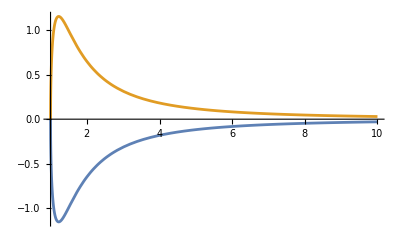

```mathematica
Plot[{terf1i[y],terf1o[y]},{y, 1,10},PlotRange->All]
```

```mathematica
terf2i[y_]:=(-aps[y]+1)/y^3 (1+1/bb)
terf2o[y_]:=(aps[y]+1)/y^3 (1+1/bb)
```

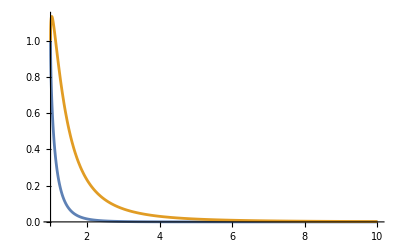

```mathematica
Plot[{terf2i[y],terf2o[y]},{y, 1,10},PlotRange->All]
```

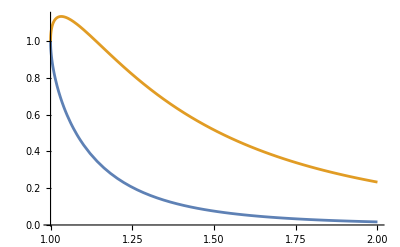

```mathematica
Plot[{terf2i[y],terf2o[y]},{y, 1,2},PlotRange->All]
```

```mathematica
terf3i[y_]:=(aps[y]^2-1)(-aps[y]+1)/(y-1/bb)
terf3o[y_]:=(aps[y]^2-1)(aps[y]+1)/(y-1/bb)
```

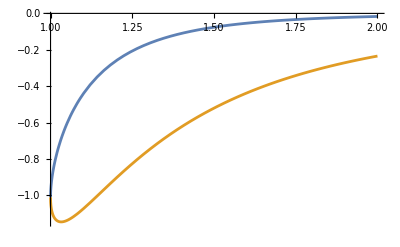

```mathematica
Plot[{terf3i[y],terf3o[y]},{y, 1,2},PlotRange->All]
```

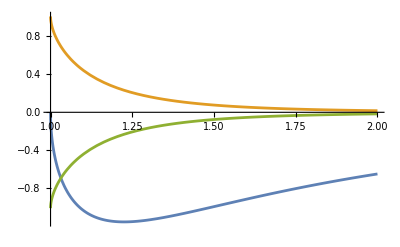

```mathematica
Plot[{terf1i[y],terf2i[y],terf3i[y]},{y, 1,2},PlotRange->All]
```

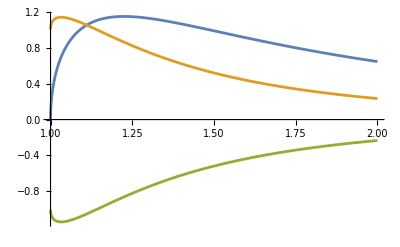

```mathematica
Plot[{terf1o[y],terf2o[y],terf3o[y]},{y, 1,2},PlotRange->All]
```

```mathematica
(****)
```

```mathematica
(*force^\theta=rhs0[λ]= -(term0+term1) s/om & rescaling/renaming*)
```

```mathematica
(*all the necessary parameters (even b3 that is not used)*)
```

```mathematica
(* up to this point nothing need to be called unless you want to see how the intermediate things look like *)
```

```mathematica
(* a for the outgoing *)
Integrate[ b/x^3 1/(2 Sqrt[2])1/Sqrt[1-b1^2/x^2],x]

(*******************)
```

(b √(1-b1^2/x^2))/(2 √2 b1^2)

Defs from Chandra

```mathematica
f[r_]:=1-rg/r
P[z_]:=z rg;
Q[z_]:=√((P[z]-rg)(P[z]+3rg));
k[z_]:=√((Q[z]-P[z]+3rg)/(2Q[z]));
𝒟[z_]:=√(P[z]^3/(P[z]-rg))
L[z_]:=𝒟[z];
B3[z_]:=(2 rg P[z])/(P[z]-rg+Q[z]);
Subscript[ϕ, 0][z_,χ_]:=2 √(P[z]/Q[z])(EllipticK[k[z]]-EllipticF[χ/2,k[z]]);
Subscript[r, 0][z_,χ_]:=1/(1/P[z]-(Q[z]-P[z]+3rg)/(4rg P[z])(1+Cos[χ]));
Subscript[x, 0][z_,χ_]:=Subscript[r, 0][z,χ]Cos[Subscript[ϕ, 0][z,χ]];
Subscript[y, 0][z_,χ_]:=Subscript[r, 0][z,χ]Sin[Subscript[ϕ, 0][z,χ]];
Subscript[χ, ∞][z_]:=2ArcSin[√((Q[z]-P[z]+rg)/(Q[z]-P[z]+3rg))];
χ[z_]:=ϵ Subscript[χ, ∞][z];
Subscript[r, in][z_]:=Subscript[r, 0][z,ϵ Subscript[χ, ∞][z]];
Subscript[ϕ, in][z_]:=Subscript[ϕ, 0][z,ϵ Subscript[χ, ∞][z]];
Subscript[rd, in][z_]:=-√(1-L[z]^2/(Subscript[r, in][z])^2(1-rg/(Subscript[r, in][z])));
Subscript[ϕd, in][z_]:=L[z]/(Subscript[r, in][z])^2;
```

Geodesic

```mathematica
kSg={(r'[λ] t'[λ])/((1-1/r[λ]) r[λ]^2)+t''[λ]==0,-r'[λ]^2/(2 (1-1/r[λ]) r[λ]^2)+((1-1/r[λ]) t'[λ]^2)/(2 r[λ]^2)-(1-1/r[λ]) r[λ] ϕ'[λ]^2+r''[λ]==0,(2 r'[λ] ϕ'[λ])/r[λ]+ϕ''[λ]==0};
kFOICg={t'[0]==1/(1-rg/(Subscript[r, in][z])),t[0]==0,r'[0]==Subscript[rd, in][z],r[0]==Subscript[r, in][z],ϕ'[0]==Subscript[ϕd, in][z],ϕ[0]==Subscript[ϕ, in][z]};
kgSubsystem=Join[kSg,kFOICg];
```

Deviation

```mathematica
ap0[λ_]:=If[ r[λ]-P[z]>10^(-18),√(1-P[z]^2/r[λ]^2),0]
rhs0f[λ_]:=(s((3 ap0[λ] Sign[r'[λ]] 𝒟[z])/(2 rg^3 r[λ]^5)-((-1+ap0[λ] Sign[r'[λ]]) (1+ap0[λ] Sign[r'[λ]])^2 𝒟[z])/(4 rg^3 z^2 (-1+r[λ]) r[λ]^3)+((1+ap0[λ] Sign[r'[λ]]) 𝒟[z]^3)/(2 rg^3 z^2 r[λ]^6)))/om
eqvar0=var''[λ]+2r'[λ]/r[λ] var'[λ] +var[λ]𝒟[z]^2/r[λ]^4-rhs0f[λ]==0;
```

```mathematica
rhs0r[λ_]:=(s((3 ap0[λ] Sign[r'[λ]] 𝒟[z])/(2 rg^3 r[λ]^5)))/om
```

```mathematica
(*^^ radial outgoing*)
```

```mathematica
eqvar1=var''[λ]+2(ap0[λ]Sign[r'[λ]])/r[λ] var'[λ] +var[λ]𝒟[z]^2/r[λ]^4-rhs0f[λ]==0;
```

Data

```mathematica
ϵ=1.001;
EE[z_]:=1;L[z_]:=𝒟[z];rg=1;z=300000.;
s=1;
om=1;
```

```mathematica
Subscript[r, in][z]
```

1.90987×10^8

## Solution and analysis

```mathematica
λmax=100000000z;
```

```mathematica
testg=NDSolve[{kgSubsystem,eqvar0,var[0]==0,var'[0]==0 },{t,r,ϕ,var},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->18,WorkingPrecision->40]
```

NDSolve::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (40.).

{{t→                                                                       13
InterpolatingFunction[{{0, 3.000000000000000000000000000000000000000 10  }}, <>],r→                                                                       13
InterpolatingFunction[{{0, 3.000000000000000000000000000000000000000 10  }}, <>],ϕ→                                                                       13
InterpolatingFunction[{{0, 3.000000000000000000000000000000000000000 10  }}, <>],var→                                                                       13
InterpolatingFunction[{{0, 3.000000000000000000000000000000000000000 10  }}, <>]}}

```mathematica
rhog[lam_]:=r[lam]/.testg[[1]]
pg[lam_]:=r'[lam]/.testg[[1]]
pgD[lam_]:=r''[lam]/.testg[[1]]
phifg[lam_]:=ϕ[lam]/.testg[[1]]
varf[lam_]:=var[lam]/.testg[[1]]
varfD[lam_]:=var'[lam]/.testg[[1]]
varfDD[lam_]:=var''[lam]/.testg[[1]]
```

```mathematica
rhog[λmax]
```

2.99981×10^13

```mathematica
apf[λ_]:=If[rhog[λ]>P[z],Sqrt[1-P[z]^2/rhog[λ]^2]Sign[pg[λ]],0]
```

```mathematica
forc[λ_]:=(s((3 apf[λ]  𝒟[z])/(2 rg^3 rhog[λ]^5)-((-1+apf[λ]) (1+apf[λ] )^2 𝒟[z])/(4 rg^3 z^2 (-1+rhog[λ]) rhog[λ]^3)+((1+apf[λ] ) 𝒟[z]^3)/(2 rg^3 z^2 rhog[λ]^6)))/om
```

```mathematica
testg1=NDSolve[{kgSubsystem,eqvar1,var[0]==0,var'[0]==0 },{t,r,ϕ,var},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12,WorkingPrecision->25]
```

NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (25.).

{{t→InterpolatingFunction[…],r→InterpolatingFunction[…],ϕ→InterpolatingFunction[…],var→InterpolatingFunction[…]}}

```mathematica
rhog1[lam_]:=r[lam]/.testg1[[1]]
pg1[lam_]:=r'[lam]/.testg1[[1]]
phifg1[lam_]:=ϕ[lam]/.testg1[[1]]
varf1[lam_]:=var[lam]/.testg1[[1]]
varf1D[lam_]:=var'[lam]/.testg1[[1]]
varf1DD[lam_]:=var''[lam]/.testg1[[1]]
```

```mathematica
FindRoot[rhog[lam]==Subscript[r, in][z],{lam,2lclo}]
```

FindRoot::srect: Value 2. lclo in search specification {lam,2 lclo} is not a number or array of numbers.

FindRoot[rhog[lam]==r_in[z],{lam,2 lclo}]

```mathematica
varf[lclo]
```

-0.000201473

```mathematica
varf[6470.367821421659]
```

0.0000100998

#### Solutions for : z = 50, om = 1

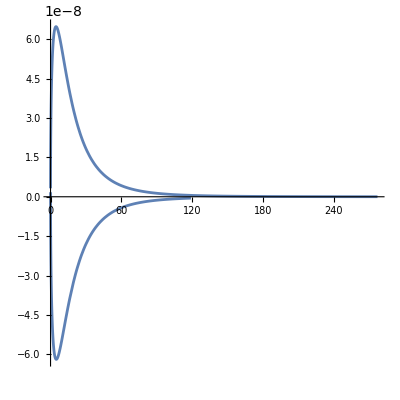

```mathematica
ParametricPlot[{rhog[lam]-z,forc[lam]},{lam,0.95 lclo,1.1 lclo},AspectRatio->1,PlotRange->All]
```

```mathematica
`
```

```mathematica
forc[lclo]
```

-2.42407×10^-7

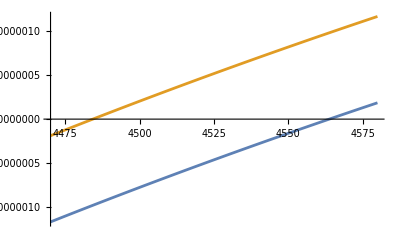

```mathematica
Plot[{varf1[lam],varf[lam]},{lam,4470, 4580},PlotRange->All]
```

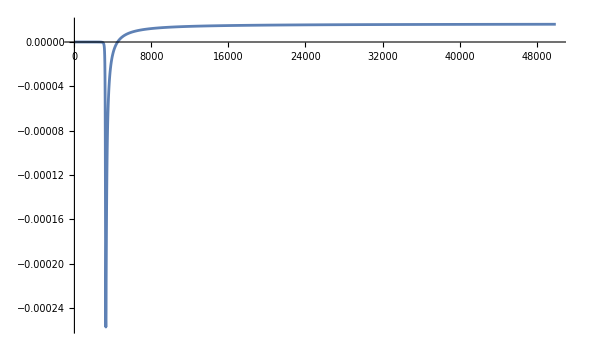

```mathematica
Plot[varf[lam],{lam,0, λmax},PlotRange->All]
```

```mathematica
varf[50000]
```

0.0000160147837557328244046122733654423886069

```mathematica
FindMinimum[varf[lam],{lam,lclo}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-0.000258306,{lam→3262.87}}

```mathematica
rhog[3262.8683190647475]
```

57.0887

#### Solutions for : z = 50, om = 1000 [1?]

```mathematica
(*the closest approach time*)
```

```mathematica
lclo=la/.FindRoot[pg[la],{la,3000}]
```

3235.18

```mathematica
rhog[lclo]-z
```

5.74985×10^-7

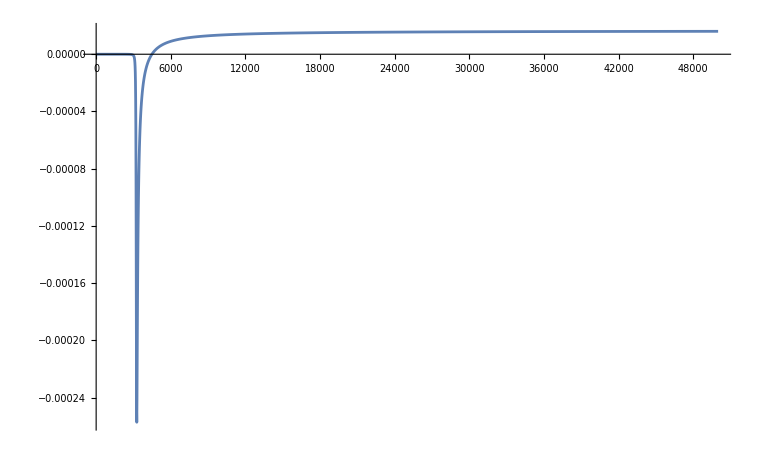

```mathematica
Plot[varf[lam],{lam,0, λmax},PlotRange->All]
```

```mathematica
varf[λmax]
```

1.64129×10^-8

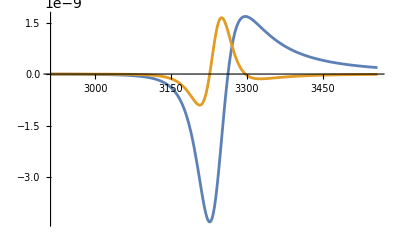

```mathematica
Plot[{varfD[lam],10varfDD[lam]},{lam,0.9lclo,1.1 lclo},PlotRange->All]
```

#### Solutions for : z = 1000, om = 1

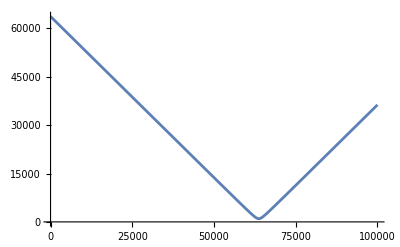

```mathematica
Plot[rhog[lam],{lam,0,100 z}]
```

```mathematica
lclo=la/.FindRoot[pg[la],{la,60000}]
```

63709.1

```mathematica
rhog[lclo]-z
```

1.99782×10^-7

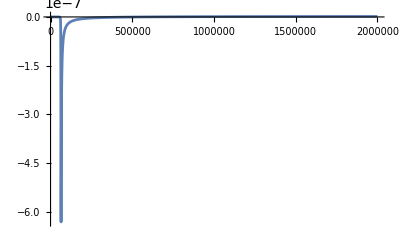

```mathematica
Plot[varf[lam],{lam,0, λmax/500},PlotRange->All]
```

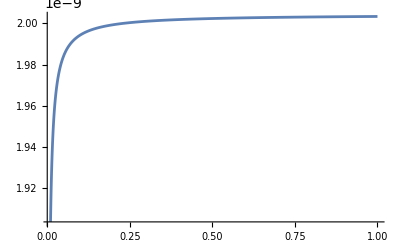

```mathematica
Plot[varf[lam],{lam, λmax/100,λmax},PlotRange->All]
```

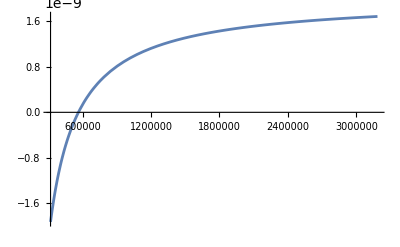

```mathematica
Plot[varf[lam],{lam,5lclo,50 lclo},PlotRange->All]
```

```mathematica
varf[λmax]
```

2.00336×10^-9

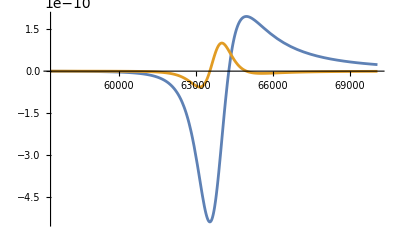

```mathematica
Plot[{varfD[lam],100varfDD[lam]},{lam,0.9lclo,1.1 lclo},PlotRange->All]
```

#### Solutions for : z = 300,000, om = 1

```mathematica
(* futher checks are needed*)
```

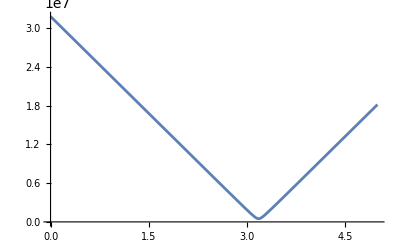

```mathematica
Plot[rhog[lam],{lam,0,100 z}]
```

```mathematica
lclo=la/.FindRoot[pg[la],{la,3 10^7}]
```

3.18284×10^7

```mathematica
rhog[lclo]/z-1
```

5.96264×10^-10

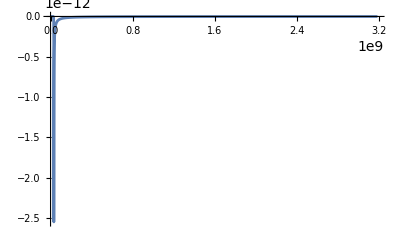

```mathematica
Plot[varf[lam],{lam,0, 100 lclo},PlotRange->All]
```

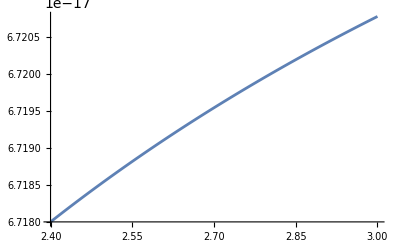

```mathematica
Plot[varf[lam],{lam, 0.8λmax,λmax},PlotRange->All]
```

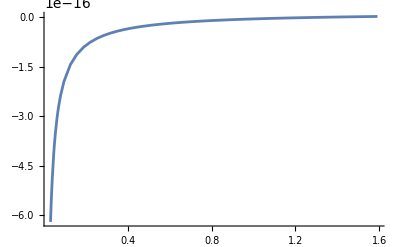

```mathematica
Plot[varf[lam],{lam,100lclo,5000 lclo},PlotRange->All]
```

```mathematica
varf[λmax]
```

2.00336×10^-9

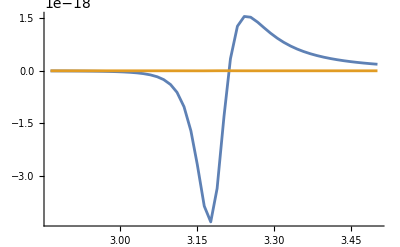

```mathematica
Plot[{varfD[lam],100varfDD[lam]},{lam,0.9lclo,1.1 lclo},PlotRange->All]
```

## Equations-parameterized geodesics chi

```mathematica
ClearAll["`*"];
```

#### assumptions & notation

Unperturbed geodesic moves in the plane θ = π/2. We take the form of the deviation  from geodesic α as in Eq (12), i.e. b3=0 approximation.
Units & names: dd = [length]=mathfrak{d}=𝒟[z]* rg, d=dd/rg=𝒟[z], b1=z=P[z]/rg, p[r] =l^r (as in Eq (2), takes both signs a1=a of Eqs (12)-(14)
 s=±1 polarization; om=ω;  λ as the affine parameter will be renamed to s in the paper, and polarization will become σ.
 var=θ-π/2=\vartheta 
 The function ap0=√(p^2) is defined with IF to avoid the possibility of complex values at the verge of the precision. May be refined. In practice p=Sign[r'[λ]]ap0[λ] 
 HERE the derivatives over the affine parameter are expressed from xi

## derivations

```mathematica
(* Up to the Chadrasekhar terms can be skipped *)
```

```mathematica
f[r_]:=1-rg/r
```

```mathematica
f[r_]:=1-rg/r
P[z_]:=z rg;
Q[z_]:=√((P[z]-rg)(P[z]+3rg));
k[z_]:=√((Q[z]-P[z]+3rg)/(2Q[z]));
𝒟[z_]:=√(P[z]^3/(P[z]-rg))
L[z_]:=𝒟[z];
B3[z_]:=(2 rg P[z])/(P[z]-rg+Q[z]);
Subscript[ϕ, 0][z_,χ_]:=2 √(P[z]/Q[z])(EllipticK[k[z]]-EllipticF[χ/2,k[z]]);
Subscript[r, 0][z_,χ_]:=1/(1/P[z]-(Q[z]-P[z]+3rg)/(4rg P[z])(1+Cos[χ]));
Subscript[x, 0][z_,χ_]:=Subscript[r, 0][z,χ]Cos[Subscript[ϕ, 0][z,χ]];
Subscript[y, 0][z_,χ_]:=Subscript[r, 0][z,χ]Sin[Subscript[ϕ, 0][z,χ]];
Subscript[χ, ∞][z_]:=2ArcSin[√((Q[z]-P[z]+rg)/(Q[z]-P[z]+3rg))];
χ[z_]:=ϵ Subscript[χ, ∞][z];
Subscript[r, in][z_]:=Subscript[r, 0][z,ϵ Subscript[χ, ∞][z]];
Subscript[ϕ, in][z_]:=Subscript[ϕ, 0][z,ϵ Subscript[χ, ∞][z]];
Subscript[rd, in][z_]:=-√(1-L[z]^2/(Subscript[r, in][z])^2(1-rg/(Subscript[r, in][z])));
Subscript[ϕd, in][z_]:=L[z]/(Subscript[r, in][z])^2;
```

```mathematica
dchdph[z_,chi_]:=-(Sqrt[Q[z]/P[z](1-k[z]^2 Sin[chi/2]^2)])
dchds[z_,chi_]:=-L[z]/Subscript[r, 0][z,chi]^2 dchdph[z,chi]
ϕot[z_]:=Subscript[ϕ, 0][z,Subscript[χ, ∞][z]];
dchds2d[z_,chi_]:=-1/(1024 rg^2 (-1+z) z^2)(3-z+√((-1+z) (3+z))) (-1-z+√((-1+z) (3+z))+(3-z+√((-1+z) (3+z))) Cos[chi])^3 (3 z+13 (-1+√((-1+z) (3+z)))+5 (3-z+√((-1+z) (3+z))) Cos[chi]) Sin[chi]
apf[z_,chi_]:=Sqrt[1-P[z]^2/Subscript[r, 0][z,chi]^2]
pf[z_,chi_]:=If[chi<Pi, -Sqrt[1-P[z]^2/Subscript[r, 0][z,chi]^2],Sqrt[1-P[z]^2/Subscript[r, 0][z,chi]^2]]
```

Geodesic

Deviation

Data

```mathematica
ϵ=1.01;
EE[z_]:=1;L[z_]:=𝒟[z];rg=1;
s=1;
om=1;
```

#### Visualisation

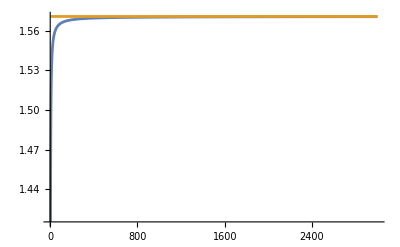

```mathematica
Plot[{Subscript[χ, ∞][z],Pi/2},{z,3,3000},PlotRange->All]
```

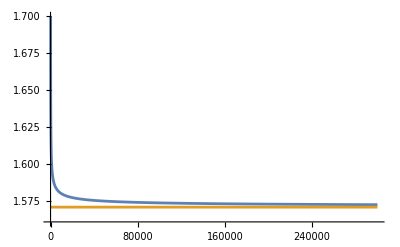

```mathematica
Plot[{ϕot[z],Pi/2},{z,3,300000},PlotRange->{Pi/2-0.01,1.7}]
```

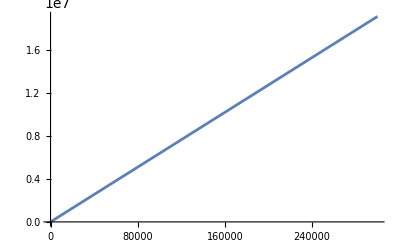

```mathematica
Plot[Subscript[r, in][z],{z,3,300000}]
```

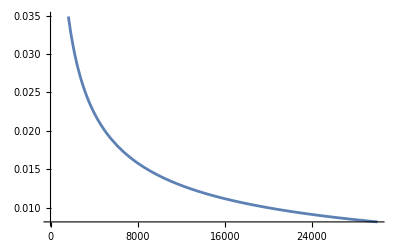

```mathematica
Plot[k[z],{z,3,30000}]
```

```mathematica
dsdchi[50.,Pi]
```

-48.9902

```mathematica
ϵ Subscript[χ, ∞][z]
```

2.02 ArcSin[√((1-z+√((-1+z) (3+z)))/(3-z+√((-1+z) (3+z))))]

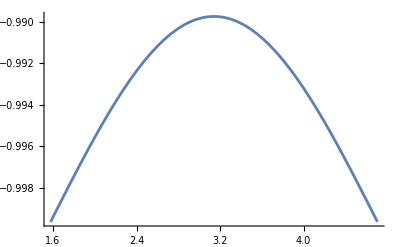

```mathematica
Plot[dphdch[50,chi],{chi,ϵ Subscript[χ, ∞][50], 2Pi -ϵ Subscript[χ, ∞][50]}]
```

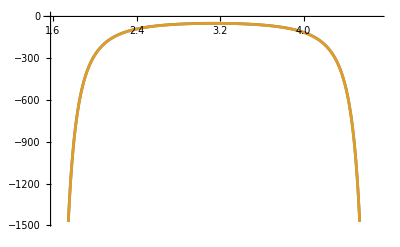

```mathematica
Plot[{jf[50,chi],-Subscript[r, 0][50,chi]^2/L[50]},{chi,ϵ Subscript[χ, ∞][50], 2Pi -ϵ Subscript[χ, ∞][50]}]
```

```mathematica
dsdchi2dchi
```

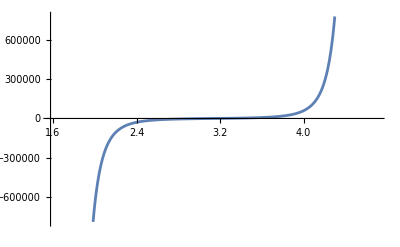

```mathematica
Plot[{jf2d[50,chi]},{chi,ϵ Subscript[χ, ∞][50], 2Pi -ϵ Subscript[χ, ∞][50]}]
```

```mathematica
{Subscript[r, in][z],Subscript[ϕ, in][z]-Pi/2}
```

{3235.07,0.123051}

```mathematica
dsfac[chi_]:=-((128 rg^4 P[z]^3 Q[z] (8 (3 rg-P[z]+Q[z])+k[z]^2 (rg (-11+9 Cos[chi])+(5-3 Cos[chi]) P[z]+(-5+3 Cos[chi]) Q[z])) Sin[chi])/(L[z]^2 (rg-3 rg Cos[chi]+(1+Cos[chi]) P[z]-(1+Cos[chi]) Q[z])^5))
```

```mathematica
Simplify[D[dsdchi[z,chi]^2,chi],Assumptions->rg>1]
```

-(64 rg^2 (-1+z) (-3+z-√(-3+2 z+z^2)) (5 z+11 (-1+√(-3+2 z+z^2))+3 (3-z+√(-3+2 z+z^2)) Cos[chi]) Sin[chi])/((-1-z+√(-3+2 z+z^2)+(3-z+√(-3+2 z+z^2)) Cos[chi])^5)

```mathematica
Simplify[Simplify[jf[z,chi],Assumptions->rg>0],z>3]
```

-(8 rg √((-1+z) (-3+z+3 √(-3+2 z+z^2)+(3-z+√(-3+2 z+z^2)) Cos[chi])))/((-1-z+√(-3+2 z+z^2)+(3-z+√(-3+2 z+z^2)) Cos[chi])^2)

```mathematica
Simplify[D[(jf[z,chi])^2,chi],Assumptions->rg>1]
```

-(64 rg^2 (-1+z) (-3+z-√(-3+2 z+z^2)) (5 z+11 (-1+√(-3+2 z+z^2))+3 (3-z+√(-3+2 z+z^2)) Cos[chi]) Sin[chi])/((-1-z+√(-3+2 z+z^2)+(3-z+√(-3+2 z+z^2)) Cos[chi])^5)

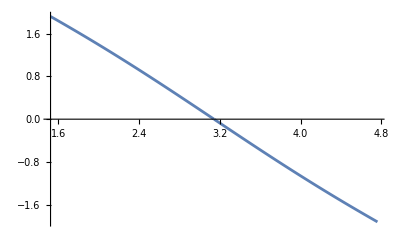

```mathematica
Plot[Subscript[ϕ, 0][10,chi],{chi,Subscript[χ, ∞][10],2Pi-Subscript[χ, ∞][10]}]
```

#### Comparisons/texts

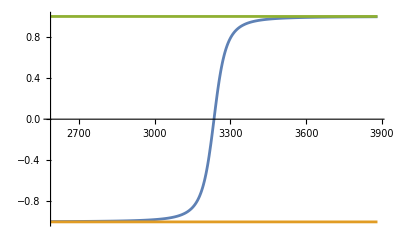

```mathematica
Plot[{pg[lam],-1,1},{lam,lclo 0.8,1.2 lclo}]
```

```mathematica
rhog[0.8 lclo]
```

648.493

```mathematica
{rhog[3500],pg[3500]}
```

{269.07778097138833279795248562631369596,0.982291831364451609454124312003720778}

```mathematica
oldpair3500={269.07778097182584419245067977682981341138`23.730035608025634,0.98229183135876798146908633081562147456`21.467529620096137}
```

```mathematica
FindRoot[Subscript[r, 0][z,chi]==rhog[0.8 lclo],{chi,4.6}]
```

{chi→4.64438}

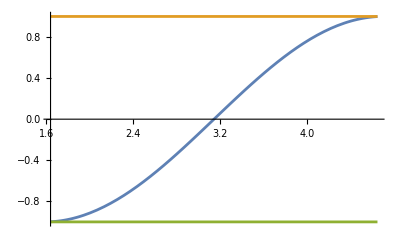

```mathematica
Plot[{drdch[chi]/jf[z,chi],1,-1}, {chi,4.6443758862249,  2 Pi-4.6443758862249}]
```

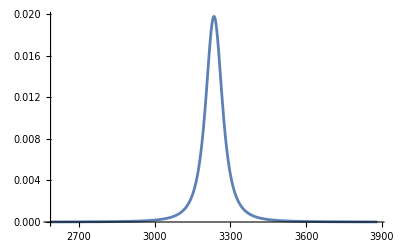

```mathematica
Plot[{pgD[lam]},{lam,lclo 0.8,1.2 lclo},PlotRange->All]
```

```mathematica
{pgD[0.8lclo],pgD[lclo]}
```

{9.33238×10^-6,0.0197959}

```mathematica
acrcs[z_,chi_]:=r0ddc[z,chi]jf[z,chi]^2+r0dc[z,chi]jf2d[z,chi]/2
```

```mathematica
acrcs[50,4.6443758862249]
```

2.95115×10^13

```mathematica
NumberForm[{Subscript[r, 0][z,chi], drdch[chi]/jf[z,chi]}/.{chi->4.533683768413148},14]
```

{269.07778097183,0.98634442992996}

```mathematica
Simplify[D[Subscript[r, 0][z,chi],chi]]
```

-(4 rg^2 z (-rg (-3+z)+√(rg^2 (-3+2 z+z^2))) Sin[chi])/((-rg (1+z)+√(rg^2 (-3+2 z+z^2))+(-rg (-3+z)+√(rg^2 (-3+2 z+z^2))) Cos[chi])^2)

```mathematica
drdch[chi_]:=-(0.01980384612481814 Sin[chi])/(0.02-0.01980384612481814 (1+Cos[chi]))^2
```

```mathematica
Simplify[D[Subscript[r, 0][z,chi],{chi,2}]]
```

(2 rg^2 z (rg (-3+z)-√(rg^2 (-3+2 z+z^2))) (2 (-rg (1+z)+√(rg^2 (-3+2 z+z^2))) Cos[chi]-(-rg (-3+z)+√(rg^2 (-3+2 z+z^2))) (-3+Cos[2 chi])))/(-rg (1+z)+√(rg^2 (-3+2 z+z^2))+(-rg (-3+z)+√(rg^2 (-3+2 z+z^2))) Cos[chi])^3

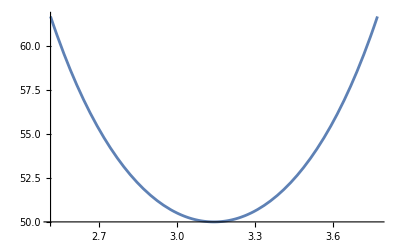

```mathematica
Plot[Subscript[r, 0][z,chi], {chi,0.8 Pi, 1.2 Pi}]
```

```mathematica
drdch[0.9Pi]
```

-16.8974

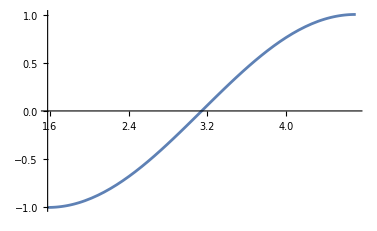

```mathematica
Plot[drdch[chi]/jf[z,chi], {chi,χ[z],  2 Pi-χ[z]}]
```

```mathematica
Plot[dphdch[z,chi],{chi,χ[z],  2 Pi-χ[z]}]
```

-Graphics-

#### auxiliar

```mathematica
FullSimplify[D[dchds[z,chi]^2,chi],Assumptions->{rg>1,z>1}]
```

-1/(1024 rg^2 (-1+z) z^2)(3-z+√((-1+z) (3+z))) (-1-z+√((-1+z) (3+z))+(3-z+√((-1+z) (3+z))) Cos[chi])^3 (3 z+13 (-1+√((-1+z) (3+z)))+5 (3-z+√((-1+z) (3+z))) Cos[chi]) Sin[chi]

```mathematica
r0dc[z_,chi_]:=-(4 rg^2 z (-rg (-3+z)+√(rg^2 (-3+2 z+z^2))) Sin[chi])/((-rg (1+z)+√(rg^2 (-3+2 z+z^2))+(-rg (-3+z)+√(rg^2 (-3+2 z+z^2))) Cos[chi])^2)
```

```mathematica
r0ddc[z_,chi_]:= (2 rg^2 z (rg (-3+z)-√(rg^2 (-3+2 z+z^2))) (2 (-rg (1+z)+√(rg^2 (-3+2 z+z^2))) Cos[chi]-(-rg (-3+z)+√(rg^2 (-3+2 z+z^2))) (-3+Cos[2 chi])))/(-rg (1+z)+√(rg^2 (-3+2 z+z^2))+(-rg (-3+z)+√(rg^2 (-3+2 z+z^2))) Cos[chi])^3
```

```mathematica
djf2=Simplify[D[jf[z,chi]^2,chi]/2]
```

-(Q[z] r_0[z,chi]^3 (-8 r_0^(0,1)[z,chi]+k[z]^2 (Sin[chi] r_0[z,chi]+8 Sin[chi/2]^2 r_0^(0,1)[z,chi])))/(4 L[z]^2 P[z])

```mathematica
rhs2chi=1/(8192 rg^2 z^(7/2))√(1/(-1+z)) (4-(3-z+√(-3+2 z+z^2)) (1+Cos[chi]))^3 ((12 (1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])^2 If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)])/rg^2+((1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])^3 (1+If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)]))/(rg (-1+z))-(32 (-1+If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)]) (1+If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)])^2)/(-1+(4 rg z)/(1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])));
```

## Equations

```mathematica
lhs2chi=var''[chi]dchds[z,chi]^2+var'[chi](2pf[z,chi]dchds[z,chi]/Subscript[r, 0][z,chi]+dchds2d[z,chi]/2)+𝒟[z]^2/Subscript[r, 0][z,chi]^4 var[chi];
```

```mathematica
Simplify[(3 ap[x] 𝒟[z])/(2 x^5)-((-1+ap[x]) (1+ap[x])^2 𝒟[z])/(4 (-1+x) x^3 z^2)+((1+ap[x]) 𝒟[z]^3)/(2 x^6 z^2)/.ap[x]->pf[z,chi]/.x->Subscript[r, 0][z,chi],Assumptions->{rg>0,z>0}]
```

1/(8192 rg^2 z^(7/2))√(1/(-1+z)) (4-(3-z+√(-3+2 z+z^2)) (1+Cos[chi]))^3 ((12 (1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])^2 If[chi<π,-√(1-P[z]^2/r_0[z,chi]^2),√(1-P[z]^2/r_0[z,chi]^2)])/rg^2+((1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])^3 (1+If[chi<π,-√(1-P[z]^2/r_0[z,chi]^2),√(1-P[z]^2/r_0[z,chi]^2)]))/(rg (-1+z))-(32 (-1+If[chi<π,-√(1-P[z]^2/r_0[z,chi]^2),√(1-P[z]^2/r_0[z,chi]^2)]) (1+If[chi<π,-√(1-P[z]^2/r_0[z,chi]^2),√(1-P[z]^2/r_0[z,chi]^2)])^2)/(-1+(4 rg z)/(1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])))

```mathematica
rf2chi[z_,chi_]:=1/(8192 rg^2 z^(7/2))√(1/(-1+z)) (4-(3-z+√(-3+2 z+z^2)) (1+Cos[chi]))^3 ((12 (1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])^2 If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)])/rg^2+((1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])^3 (1+If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)]))/(rg (-1+z))-(32 (-1+If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)]) (1+If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)])^2)/(-1+(4 rg z)/(1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])))
```

```mathematica
Simplify[(3 ap[x] 𝒟[z])/(2 x^5)/.ap[x]->pf[z,chi]/.x->Subscript[r, 0][z,chi],Assumptions->{rg>0,z>0}]
```

(3 √(1/(-1+z)) (1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])^5 If[chi<π,-√(1-P[z]^2/r_0[z,chi]^2),√(1-P[z]^2/r_0[z,chi]^2)])/(2048 rg^4 z^(7/2))

```mathematica
rf2chiR[z_,chi_]:=(3 √(1/(-1+z)) (1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])^5 If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)])/(2048 rg^4 z^(7/2))
```

```mathematica
(*^^ radial out*)
```

## Solution and analysis

```mathematica
ϵ=1.0001;
epout=1.;
chimax=2Pi-epout Subscript[χ, ∞][z];
EE[z_]:=1;L[z_]:=𝒟[z];rg=1;
s=1;
om=1; 
z=300000.;
```

```mathematica
bounds={ Subscript[χ, ∞][z],2Pi- Subscript[χ, ∞][z]}
```

{1.56089,4.72229}

```mathematica
chim[de_]:=2Pi-(1+de)epout Subscript[χ, ∞][z]
```

```mathematica
chim[10^-8]
```

4.71239

```mathematica
χ[z]
```

1.5765

```mathematica
chimax
```

4.72229

```mathematica
Subscript[r, 0][z,chim[10^-10]]
```

1.90986×10^15

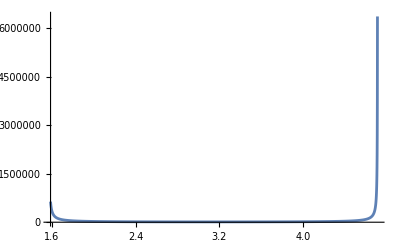

```mathematica
Plot[Subscript[r, 0][z,chi],{chi,χ[z],chimax},PlotRange->All]
```

```mathematica
sol2dchi=NDSolve[{lhs2chi==rf2chi[z,chi],var[χ[z]]==0,var'[χ[z]]==0 },{var},{chi,χ[z], chimax},AccuracyGoal->20,PrecisionGoal->12,WorkingPrecision->40]
```

NDSolve::precw: The precision of the differential equation ({{9.00003×10^10 (3.33333×10^-6+Times[«2»])^4 var[chi]+(600002. Power[«2»] If[«3»] Power[«2»]-7.23381×10^-20 Power[«2»] Plus[«2»] Sin[«1»]) var'[chi]+9.00006×10^10 (3.33333×10^-6+Times[«2»])^4 (1-6.66663×10^-6 Power[«2»]) var''[chi]==1.50704×10^-26 (4-3.99999 Plus[«2»])^3 (12 Plus[«2»]^2 If[Less[«2»],Times[«2»],√(«1»)]+3.33334×10^-6 Plus[«2»]^3 (1+If[«3»])-(32 (-1+If[«3»]) Plus[«2»]^2)/Plus[«2»]),var[1.57095]==0,var'[1.57095]==0},{},{},{},{}}) is less than WorkingPrecision (40.).

{{var→InterpolatingFunction[…]}}

```mathematica
chimax
```

4.71244

```mathematica
bounds[[2]]-chimax
```

1.57079×10^-8

```mathematica
bounds[[2]]-4.7123906470474224901039702475060876342505401099357980276115432296449823970471
```

0.

```mathematica
var2c[chi_]:=var[chi]/.sol2dchi[[1]]
var2cd[chi_]:=var'[chi]/.sol2dchi[[1]]
var2cdd[chi_]:=var''[chi]/.sol2dchi[[1]]
```

```mathematica
Subscript[r, 0][z,chim[10^-12]]
```

1.90972×10^17

### Pictures

#### Pictures & ct : ϵ = 1.01; epout = 1.001; z = 300000

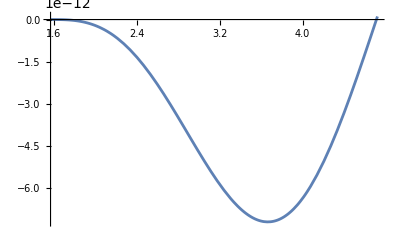

```mathematica
Plot[var2c[chi],{chi,χ[z],chimax},PlotRange->All]
```

```mathematica
{"χmax=",chi,var2c[chim[10^-12]],var2cd[chim[10^-12]],var2cdd[chim[10^-12]]}
```

{χmax=,chi,6.96743×10^-17,1.11111×10^-11,-8.87002×10^-17}

```mathematica
{"χmax=",chi,var2c[chi],var2cd[chi],var2cdd[chi]}/.chi->chimax
```

{χmax=,4.71239,9.11942×10^-17,-1.52584×10^-9,-5.20805×10^6}

```mathematica
{"χmax=",chi,var2c[chi],var2cd[chi],var2cdd[chi]}/.chi->chimax
```

{χmax=,4.71239,8.94492×10^-17,1.11091×10^-11,7.30241×10^-14}

#### Pictures & ct : ϵ = 1.01; epout = 1.001; z = 10000

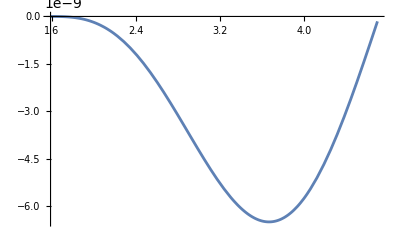

```mathematica
Plot[var2c[chi],{chi,χ[z],2Pi-χ[z]},PlotRange->All]
```

```mathematica
{"χmax=",chi,var2c[chi],var2cd[chi],var2cdd[chi]}/.chi->chimax
```

{χmax=,4.71244,1.88486×10^-12,9.99897×10^-9,-1.22823×10^-12}

```mathematica
{"χmax=",chi,var2c[chi],var2cd[chi],var2cdd[chi]}/.chi->chimax
```

{χmax=,4.71242,1.7435×10^-12,9.99897×10^-9,-1.9966×10^-12}

#### Pictures & ct : ϵ = 1.01; epout = 1.001; z = 50

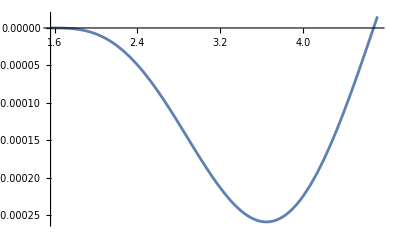

```mathematica
Plot[var2c[chi],{chi,χ[z],2Pi-χ[z]},PlotRange->All]
```

```mathematica
{"χmax=",chi,var2c[chi(1-10^(-9))],var2cd[chi(1-10^(-9))],var2cdd[chi(1-10^(-9))]}/.chi->chimax
```

{χmax=,4.72229,0.0000154517,0.000406542,10.3279}

```mathematica
{"χmax=",chi,var2c[chi],var2cd[chi],var2cdd[chi]}/.chi->chimax
```

{χmax=,4.72073,0.0000148154,0.000406497,-0.0000179426}

```mathematica
{"χmax=",chi,var2c[chi],var2cd[chi],var2cdd[chi]}/.chi->chimax
```

{χmax=,4.72228,0.0000154435,0.000406469,-0.0000194667}

```mathematica
FindMinimum[{var2c[chi],3<chi<6},{chi,Pi}]
```

{-0.000258958,{chi→3.6484}}

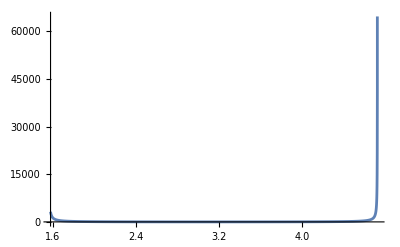

```mathematica
Plot[Subscript[r, 0][z,chi],{chi,χ[z],chimax},PlotRange->{50,Subscript[r, 0][z,chimax]/5}]
```

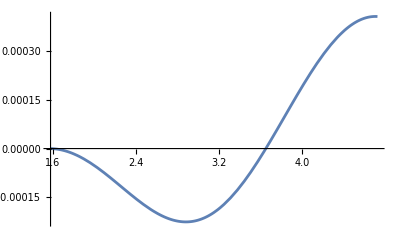

```mathematica
Plot[var2cd[chi],{chi,χ[z],chimax},PlotRange->All]
```

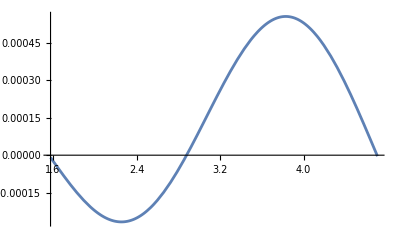

```mathematica
Plot[var2cdd[chi],{chi,χ[z],2Pi-χ[z]},PlotRange->All]
```

## Iterative solution - numerical on chi parameterization

#### Solutions for : z = 50, om = 1 IC !!!

```mathematica
ϵ=1.01;
epout=1.0001;
chimax=2Pi-epout Subscript[χ, ∞][z];
EE[z_]:=1;L[z_]:=𝒟[z];rg=1;
s=1;
om=1; 
z=50.;
```

```mathematica
lhs2chi0=var''[chi]dchds[z,chi]^2+var'[chi](2pf[z,chi]dchds[z,chi]/Subscript[r, 0][z,chi]+dchds2d[z,chi]/2);
rf2chi[z_,chi_]:=1/(8192 rg^2 z^(7/2))√(1/(-1+z)) (4-(3-z+√(-3+2 z+z^2)) (1+Cos[chi]))^3 ((12 (1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])^2 If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)])/rg^2+((1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])^3 (1+If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)]))/(rg (-1+z))-(32 (-1+If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)]) (1+If[chi<π,-√(1-P[z]^2/(Subscript[r, 0][z,chi])^2),√(1-P[z]^2/(Subscript[r, 0][z,chi])^2)])^2)/(-1+(4 rg z)/(1+z-√(-3+2 z+z^2)+(-3+z-√(-3+2 z+z^2)) Cos[chi])))
```

```mathematica
stu0c=NDSolve[{lhs2chi0==rf2chi[z,chi],var[χ[z]]==0,var'[χ[z]]==0 },{var},{chi,χ[z], chimax},AccuracyGoal->20,PrecisionGoal->14,WorkingPrecision->30]
```

NDSolve::precw: The precision of the differential equation ({{(101.981 Power[«2»] If[«3»] Power[«2»]-1.57875×10^-8 Power[«2»] Plus[«2»] Sin[«1»]) var'[chi]+2600.04 (0.02+Times[«2»])^4 (1-0.038861 Power[«2»]) var''[chi]==1.97295×10^-11 (4-3.96077 Plus[«2»])^3 (12 Plus[«2»]^2 If[Less[«2»],Times[«2»],√(«1»)]+0.0204082 Plus[«2»]^3 (1+If[«3»])-(32 (-1+If[«3»]) Plus[«2»]^2)/Plus[«2»]),var[1.5765]==0,var'[1.5765]==0},{},{},{},{}}) is less than WorkingPrecision (30.).

{{var→InterpolatingFunction[…]}}

```mathematica
(* stu0=NDSolve[{te''[t]+2/Sqrt[1+t^2]te'[t] t/(t^2)^(1/4)==t/(t^2)^(1/4) 0.01/(1+t^2)^2,te[-10.]==0,te'[-10.]==0},{te},{t,-10,200}] *)
```

```mathematica
tefc0[t_]:=var[t]/.stu0c[[1]]
tefcd0[t_]:=var'[t]/.stu0c[[1]]
tefcdd0[t_]:=var''[t]/.stu0c[[1]]
```

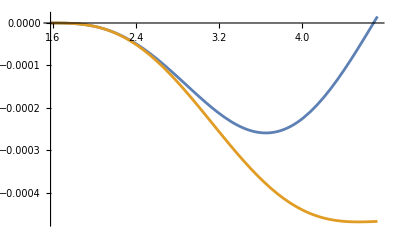

```mathematica
Plot[{var2c[chi],tefc0[chi]},{chi,χ[z],chimax},PlotRange->All]
```

```mathematica
tefc0[Pi]
```

-0.0002390420636013349763163338814

```mathematica
-tefcd0[Pi]*dchds[z,Pi]
```

-5.28343×10^-6

```mathematica
(* te''[λ]+2r'[λ]/r[λ] te'[λ] +tef0[λ]𝒟[z]^2/r[λ]^4==0*)
```

```mathematica
stu1c=NDSolve[{var''[chi]dchds[z,chi]^2+var'[chi](2pf[z,chi]dchds[z,chi]/Subscript[r, 0][z,chi]+dchds2d[z,chi]/2)+𝒟[z]^2/Subscript[r, 0][z,chi]^4 tefc0[chi]==0,var[χ[z]]==0,var'[χ[z]]==0 },{var},{chi,χ[z], chimax},AccuracyGoal->20,PrecisionGoal->14,WorkingPrecision->30]
```

NDSolve::precw: The precision of the differential equation ({{2551.02 (0.02+Times[«2»])^4 InterpolatingFunction[{{«2»}},{5,3,2,{«1»},{«1»},0,0,0,0,Automatic,«3»},{{«291»}},{{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},«281»},{Automatic}][chi]+(101.981 Power[«2»] If[«3»] Power[«2»]-1.57875×10^-8 Power[«2»] Plus[«2»] Sin[«1»]) var'[chi]+2600.04 (0.02+Times[«2»])^4 (1-0.038861 Power[«2»]) var''[chi]==0,var[1.5765]==0,var'[1.5765]==0},{},{},{},{}}) is less than WorkingPrecision (30.).

{{var→InterpolatingFunction[…]}}

```mathematica
tefc1[t_]:=var[t]/.stu1c[[1]]
tefcd1[t_]:=var'[t]/.stu1c[[1]]
tefcdd1[t_]:=var''[t]/.stu1c[[1]]
```

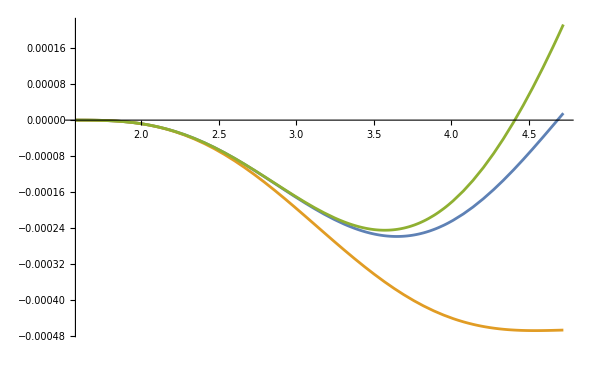

```mathematica
Plot[{var2c[chi],tefc0[chi],tefc0[chi]+tefc1[chi]},{chi,χ[z],chimax},PlotRange->All]
```

```mathematica
stu2c=NDSolve[{var''[chi]dchds[z,chi]^2+var'[chi](2pf[z,chi]dchds[z,chi]/Subscript[r, 0][z,chi]+dchds2d[z,chi]/2)+𝒟[z]^2/Subscript[r, 0][z,chi]^4 tefc1[chi]==0,var[χ[z]]==0,var'[χ[z]]==0 },{var},{chi,χ[z], chimax},AccuracyGoal->20,PrecisionGoal->14,WorkingPrecision->30]
```

NDSolve::precw: The precision of the differential equation ({{2551.02 (0.02+Times[«2»])^4 InterpolatingFunction[{{«2»}},{5,3,2,{«1»},{«1»},0,0,0,0,Automatic,«3»},{{«249»}},{{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},«239»},{Automatic}][chi]+(101.981 Power[«2»] If[«3»] Power[«2»]-1.57875×10^-8 Power[«2»] Plus[«2»] Sin[«1»]) var'[chi]+2600.04 (0.02+Times[«2»])^4 (1-0.038861 Power[«2»]) var''[chi]==0,var[1.5765]==0,var'[1.5765]==0},{},{},{},{}}) is less than WorkingPrecision (30.).

{{var→InterpolatingFunction[…]}}

```mathematica
tefc2[t_]:=var[t]/.stu2c[[1]]
tef2cd[t_]:=var'[t]/.stu2c[[1]]
tefc2dd[t_]:=var''[t]/.stu2c[[1]]
```

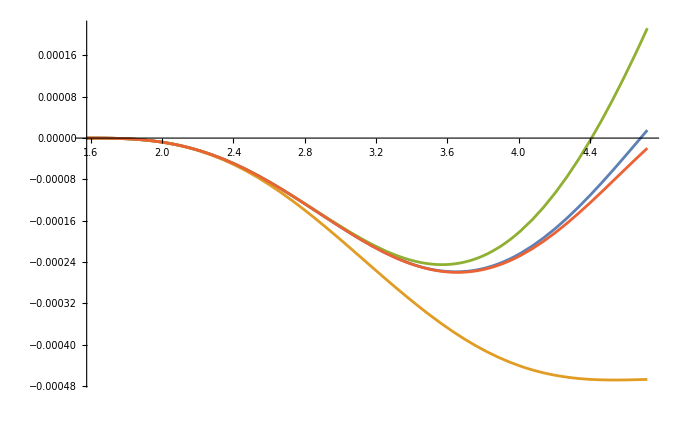

```mathematica
Plot[{var2c[chi],tefc0[chi],tefc0[chi]+tefc1[chi],tefc0[chi]+tefc1[chi]+tefc2[chi]},{chi,χ[z],chimax},PlotRange->All]
```

```mathematica
stu3c=NDSolve[{var''[chi]dchds[z,chi]^2+var'[chi](2pf[z,chi]dchds[z,chi]/Subscript[r, 0][z,chi]+dchds2d[z,chi]/2)+𝒟[z]^2/Subscript[r, 0][z,chi]^4 tefc2[chi]==0,var[χ[z]]==0,var'[χ[z]]==0 },{var},{chi,χ[z], chimax},AccuracyGoal->20,PrecisionGoal->14,WorkingPrecision->30]
```

NDSolve::precw: The precision of the differential equation ({{2551.02 (0.02+Times[«2»])^4 InterpolatingFunction[{{«2»}},{5,3,2,{«1»},{«1»},0,0,0,0,Automatic,«3»},{{«257»}},{{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},{«3»},«247»},{Automatic}][chi]+(101.981 Power[«2»] If[«3»] Power[«2»]-1.57875×10^-8 Power[«2»] Plus[«2»] Sin[«1»]) var'[chi]+2600.04 (0.02+Times[«2»])^4 (1-0.038861 Power[«2»]) var''[chi]==0,var[1.5765]==0,var'[1.5765]==0},{},{},{},{}}) is less than WorkingPrecision (30.).

{{var→InterpolatingFunction[…]}}

```mathematica
tefc3[t_]:=var[t]/.stu3c[[1]]
tef3cd[t_]:=var'[t]/.stu3c[[1]]
tefc3dd[t_]:=var''[t]/.stu3c[[1]]
```

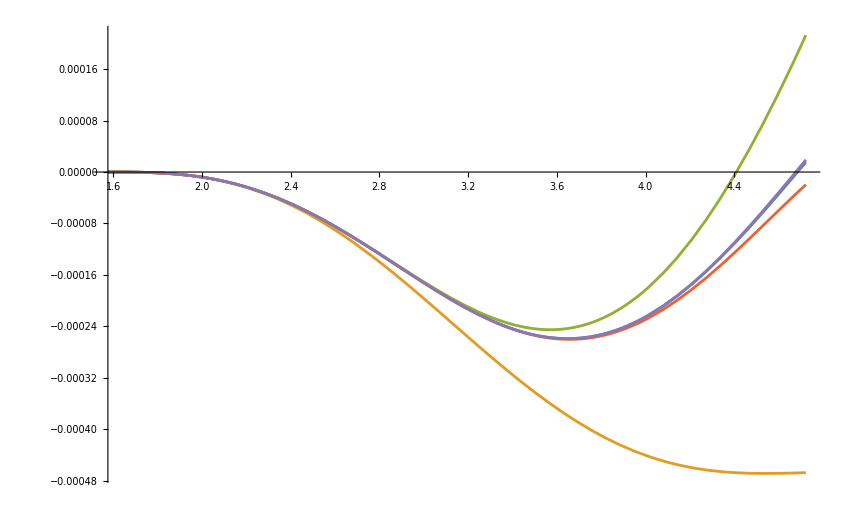

```mathematica
Plot[{var2c[chi],tefc0[chi],tefc0[chi]+tefc1[chi],tefc0[chi]+tefc1[chi]+tefc2[chi],tefc0[chi]+tefc1[chi]+tefc2[chi]+tefc3[chi]},{chi,χ[z],chimax},PlotRange->All]
```

```mathematica
Plot[{var2c[chi],tefc0[chi],tefc0[chi]+tefc1[chi],tefc0[chi]+tefc1[chi]+tefc2[chi],tefc0[chi]+tefc1[chi]+tefc2[chi]+tefc3[chi]},{chi,4.6,chimax},PlotRange->{-0.0001,0.00015}]
```

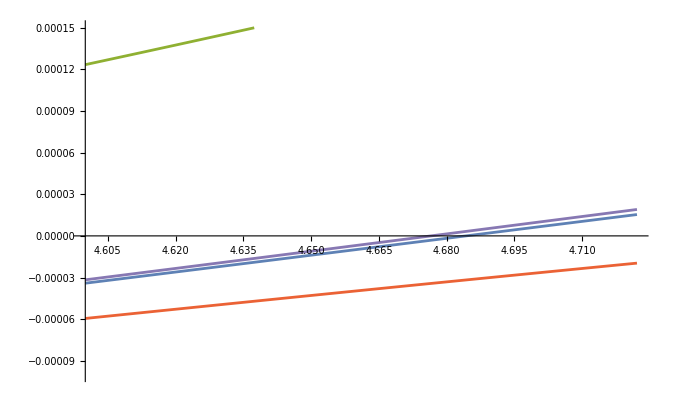

## Iterative solution - numerical (affine par)

#### Solutions for : z = 50, om = 1 IC !!!

```mathematica
ϵ=1.01;
EE[z_]:=1;L[z_]:=𝒟[z];rg=1;z=50.;
s=1;
om=1;
```

```mathematica
λmax=1000z
```

50000.

```mathematica
eqvar0stu=var''[λ]+2r'[λ]/r[λ] var'[λ] -rhs0f[λ]==0;
```

```mathematica
stu0=NDSolve[{kgSubsystem,eqvar0stu,var[0]==0,var'[0]==0 },{t,r,ϕ,var},{λ,0,λmax},AccuracyGoal->16,PrecisionGoal->13]
```

{{t→InterpolatingFunction[…],r→InterpolatingFunction[…],ϕ→InterpolatingFunction[…],var→InterpolatingFunction[…]}}

```mathematica
(* stu0=NDSolve[{te''[t]+2/Sqrt[1+t^2]te'[t] t/(t^2)^(1/4)==t/(t^2)^(1/4) 0.01/(1+t^2)^2,te[-10.]==0,te'[-10.]==0},{te},{t,-10,200}] *)
```

```mathematica
tef0[t_]:=var[t]/.stu0[[1]]
tefd0[t_]:=var'[t]/.stu0[[1]]
tefdd0[t_]:=var''[t]/.stu0[[1]]
```

```mathematica
tef0[λmax]
```

-0.00046623

```mathematica
rhog[lam_]:=r[lam]/.stu0[[1]]
pg[lam_]:=r'[lam]/.stu0[[1]]
```

```mathematica
lclo=FindRoot[pg[lam],{lam,3000},AccuracyGoal->16,PrecisionGoal->13]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{lam→3235.18}

```mathematica
FindRoot[1-z^2/rhog[lam]^2,{lam,3000}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{lam→3235.18}

```mathematica
tef0[3235.183910709575]
```

-0.000238502

```mathematica
tefd0[3235.183910709575]
```

-6.03698×10^-6

```mathematica
(*^z=10000^*)
```

```mathematica
(* te''[λ]+2r'[λ]/r[λ] te'[λ] +tef0[λ]𝒟[z]^2/r[λ]^4==0*)
```

```mathematica
kgSubsystem
```

{(r'[λ] t'[λ])/((1-1/r[λ]) r[λ]^2)+t''[λ]==0,-r'[λ]^2/(2 (1-1/r[λ]) r[λ]^2)+((1-1/r[λ]) t'[λ]^2)/(2 r[λ]^2)-(1-1/r[λ]) r[λ] ϕ'[λ]^2+r''[λ]==0,(2 r'[λ] ϕ'[λ])/r[λ]+ϕ''[λ]==0,t'[0]==1.00031,t[0]==0,r'[0]==-0.999878,r[0]==3235.07,ϕ'[0]==4.82604×10^-6,ϕ[0]==1.69385}

```mathematica
stu1=NDSolve[{kgSubsystem,te''[λ]+2r'[λ]/r[λ] te'[λ] +tef0[λ]𝒟[z]^2/r[λ]^4==0,te[0]==0,te'[0]==0 },{t,r,ϕ,te},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

{{t→InterpolatingFunction[…],r→InterpolatingFunction[…],ϕ→InterpolatingFunction[…],te→InterpolatingFunction[…]}}

```mathematica
tef1[t_]:=te[t]/.stu1[[1]]
tefd1[t_]:=te'[t]/.stu1[[1]]
tefdd1[t_]:=te''[t]/.stu1[[1]]
```

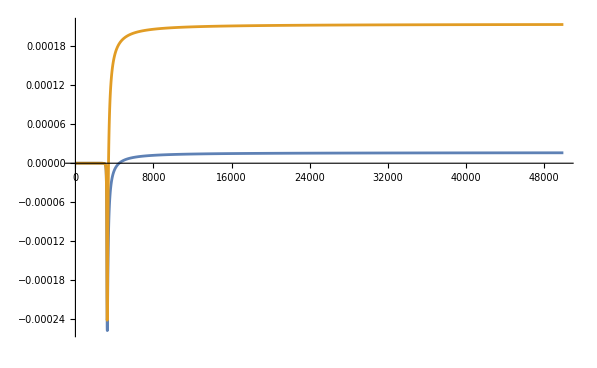

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]},{lam,0,λmax},PlotRange->All]
```

```mathematica
stu2=NDSolve[{kgSubsystem,te''[λ]+2r'[λ]/r[λ] te'[λ] +tef1[λ]𝒟[z]^2/r[λ]^4==0,te[0]==0,te'[0]==0 },{t,r,ϕ,te},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

{{t→InterpolatingFunction[…],r→InterpolatingFunction[…],ϕ→InterpolatingFunction[…],te→InterpolatingFunction[…]}}

```mathematica
tef2[t_]:=te[t]/.stu2[[1]]
tefd2[t_]:=te'[t]/.stu2[[1]]
tefdd2[t_]:=te''[t]/.stu2[[1]]
```

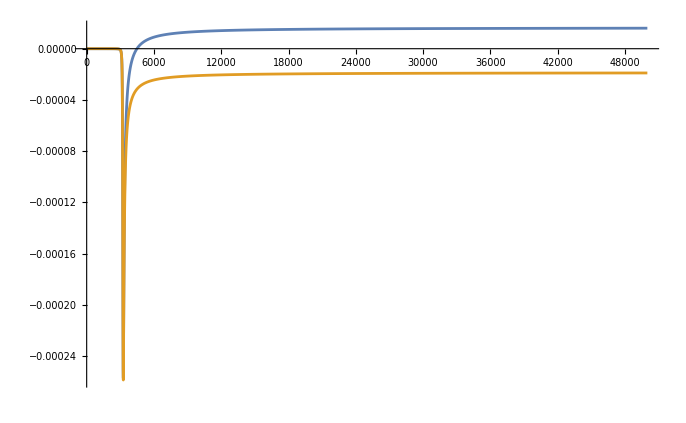

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]},{lam,0,λmax},PlotRange->All]
```

```mathematica
stu3=NDSolve[{kgSubsystem,te''[λ]+2r'[λ]/r[λ] te'[λ] +tef2[λ]𝒟[z]^2/r[λ]^4==0,te[0]==0,te'[0]==0 },{t,r,ϕ,te},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

{{t→InterpolatingFunction[…],r→InterpolatingFunction[…],ϕ→InterpolatingFunction[…],te→InterpolatingFunction[…]}}

```mathematica
tef3[t_]:=te[t]/.stu3[[1]]
tefd3[t_]:=te'[t]/.stu3[[1]]
tefdd3[t_]:=te''[t]/.stu3[[1]]
```

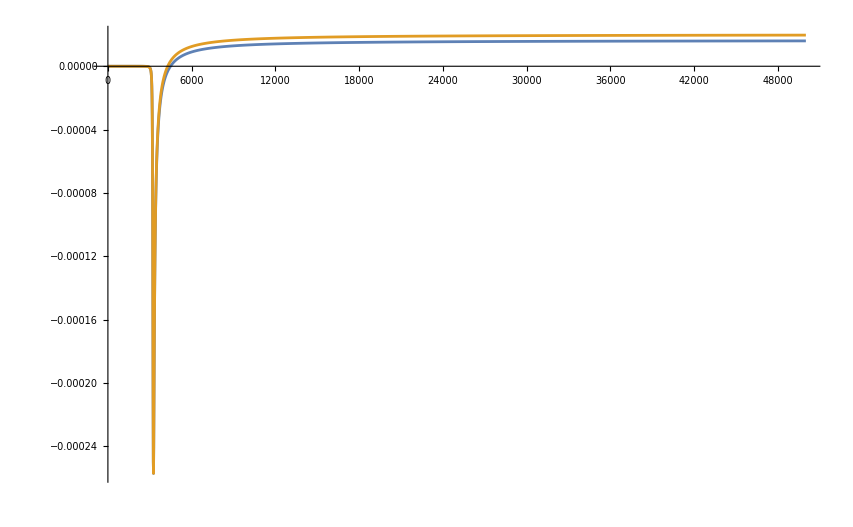

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]},{lam,0,λmax},PlotRange->All]
```

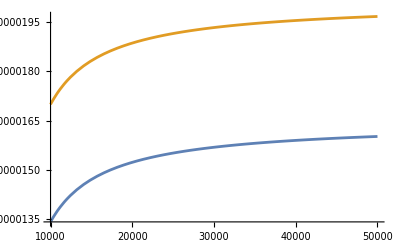

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]},{lam,λmax/5,λmax},PlotRange->All]
```

```mathematica
stu4=NDSolve[{kgSubsystem,te''[λ]+2r'[λ]/r[λ] te'[λ] +tef3[λ]𝒟[z]^2/r[λ]^4==0,te[0]==0,te'[0]==0 },{t,r,ϕ,te},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

{{t→InterpolatingFunction[…],r→InterpolatingFunction[…],ϕ→InterpolatingFunction[…],te→InterpolatingFunction[…]}}

```mathematica
tef4[t_]:=te[t]/.stu4[[1]]
tefd4[t_]:=te'[t]/.stu4[[1]]
tefdd4[t_]:=te''[t]/.stu4[[1]]
```

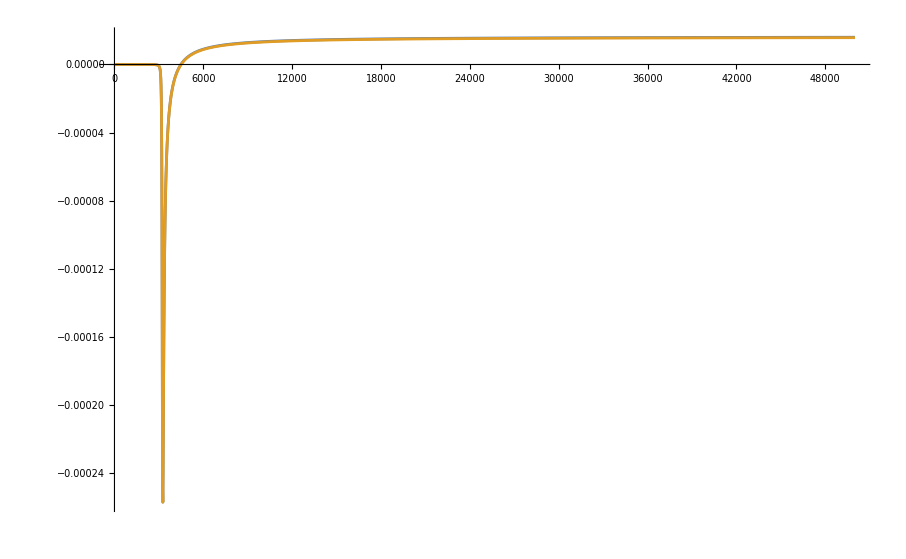

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]},{lam,0,λmax},PlotRange->All]
```

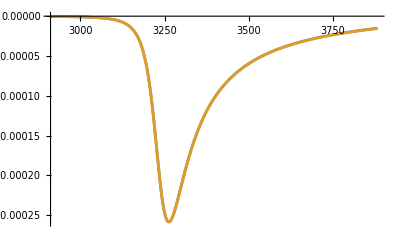

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]},{lam,0.9 lclo,1.2lclo},PlotRange->All]
```

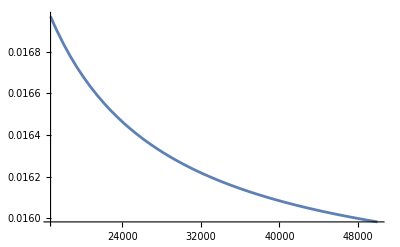

```mathematica
Plot[{1-(tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam])/varf[lam]},{lam,λmax/3,λmax},PlotRange->All]
```

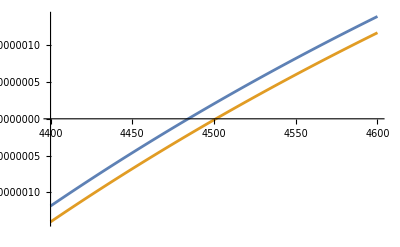

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]},{lam,4400,4600},PlotRange->All]
```

#### Solutions for : z = 50, om = 1

```mathematica
ϵ=1.01;
EE[z_]:=1;L[z_]:=𝒟[z];rg=1;z=50.;
s=1;
om=1;
```

```mathematica
λmax=1000z
```

50000.

```mathematica
eqvar0stu=var''[λ]+2r'[λ]/r[λ] var'[λ] -rhs0f[λ]==0;
```

```mathematica
stu0=NDSolve[{kgSubsystem,eqvar0stu,var[0]==0,var'[0]==0 },{t,r,ϕ,var},{λ,0,λmax},AccuracyGoal->16,PrecisionGoal->13]
```

NDSolve::deqn: Equation or list of equations expected instead of kgSubsystem in the first argument {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}.

NDSolve[{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0},{t,r,ϕ,var},{λ,0,50000.},AccuracyGoal→16,PrecisionGoal→13]

```mathematica
(* stu0=NDSolve[{te''[t]+2/Sqrt[1+t^2]te'[t] t/(t^2)^(1/4)==t/(t^2)^(1/4) 0.01/(1+t^2)^2,te[-10.]==0,te'[-10.]==0},{te},{t,-10,200}] *)
```

```mathematica
tef0[t_]:=var[t]/.stu0[[1]]
tefd0[t_]:=var'[t]/.stu0[[1]]
tefdd0[t_]:=var''[t]/.stu0[[1]]
```

```mathematica
tef0[15000.]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

var[15000.]/.{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}

```mathematica
Plot[{varf[lam],tef0[lam]},{lam,0,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,-1. rhs0f[λ]+(2. r'[λ] var'[λ])/r[λ]+var''[λ]==0.,var[0.]==0.,var'[0.]==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[tefd0[lam],{lam,0,λmax/10},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,-1. rhs0f[λ]+(2. r'[λ] var'[λ])/r[λ]+var''[λ]==0.,var[0.]==0.,var'[0.]==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
(* te''[λ]+2r'[λ]/r[λ] te'[λ] +tef0[λ]𝒟[z]^2/r[λ]^4==0*)
```

```mathematica
stu1=NDSolve[{kgSubsystem,te''[λ]+2r'[λ]/r[λ] te'[λ] +tef0[λ]𝒟[z]^2/r[λ]^4==0,te[0]==0,te'[0]==0 },{t,r,ϕ,te},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of kgSubsystem in the first argument {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}.

NDSolve[{kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0},{t,r,ϕ,te},{λ,0,50000.},AccuracyGoal→20,PrecisionGoal→12]

```mathematica
tef1[t_]:=te[t]/.stu1[[1]]
tefd1[t_]:=te'[t]/.stu1[[1]]
tefdd1[t_]:=te''[t]/.stu1[[1]]
```

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]},{lam,0,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,-1. rhs0f[λ]+(2. r'[λ] var'[λ])/r[λ]+var''[λ]==0.,var[0.]==0.,var'[0.]==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
stu2=NDSolve[{kgSubsystem,te''[λ]+2r'[λ]/r[λ] te'[λ] +tef1[λ]𝒟[z]^2/r[λ]^4==0,te[0]==0,te'[0]==0 },{t,r,ϕ,te},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of kgSubsystem in the first argument {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}.

NDSolve[{kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0},{t,r,ϕ,te},{λ,0,50000.},AccuracyGoal→20,PrecisionGoal→12]

```mathematica
tef2[t_]:=te[t]/.stu2[[1]]
tefd2[t_]:=te'[t]/.stu2[[1]]
tefdd2[t_]:=te''[t]/.stu2[[1]]
```

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]},{lam,0,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
stu3=NDSolve[{kgSubsystem,te''[λ]+2r'[λ]/r[λ] te'[λ] +tef2[λ]𝒟[z]^2/r[λ]^4==0,te[0]==0,te'[0]==0 },{t,r,ϕ,te},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of kgSubsystem in the first argument {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}.

NDSolve[{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0},{t,r,ϕ,te},{λ,0,50000.},AccuracyGoal→20,PrecisionGoal→12]

```mathematica
tef3[t_]:=te[t]/.stu3[[1]]
tefd3[t_]:=te'[t]/.stu3[[1]]
tefdd3[t_]:=te''[t]/.stu3[[1]]
```

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]},{lam,0,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]},{lam,λmax/5,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
stu4=NDSolve[{kgSubsystem,te''[λ]+2r'[λ]/r[λ] te'[λ] +tef3[λ]𝒟[z]^2/r[λ]^4==0,te[0]==0,te'[0]==0 },{t,r,ϕ,te},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of kgSubsystem in the first argument {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}.

NDSolve[{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0},{t,r,ϕ,te},{λ,0,50000.},AccuracyGoal→20,PrecisionGoal→12]

```mathematica
tef4[t_]:=te[t]/.stu4[[1]]
tefd4[t_]:=te'[t]/.stu4[[1]]
tefdd4[t_]:=te''[t]/.stu4[[1]]
```

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]},{lam,0,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]},{lam,0.9 lclo,1.2lclo},PlotRange->All]
```

Plot::plln: Limiting value 0.9 lclo in {lam,0.9 lclo,1.2 lclo} is not a machine-sized real number.

Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]},{lam,0.9 lclo,1.2 lclo},PlotRange→All]

```mathematica
Plot[{1-(tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam])/varf[lam]},{lam,λmax/3,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]},{lam,4400,4600},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[{tef[t],tef0[t],tef0[t]+tef1[t],tef0[t]+tef1[t]+tef2[t],tef0[t]+tef1[t]+tef2[t]+tef3[t]},{t,-tin,tend}]
```

Plot::plln: Limiting value -tin in {t,-tin,tend} is not a machine-sized real number.

Plot[{tef[t],tef0[t],tef0[t]+tef1[t],tef0[t]+tef1[t]+tef2[t],tef0[t]+tef1[t]+tef2[t]+tef3[t]},{t,-tin,tend}]

#### Solutions for : z = 10000, om = 1

```mathematica
lclo=la/.FindRoot[pg[la],{la,600000}]
```

FindRoot::nlnum: The function value {pg[600000.]} is not a list of numbers with dimensions {1} at {la} = {600000.}.

ReplaceAll::reps: {FindRoot[pg[la],{la,600000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {pg[600000.]} is not a list of numbers with dimensions {1} at {la} = {600000.}.

ReplaceAll::reps: {FindRoot[pg[la],{la,600000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

la/.FindRoot[pg[la],{la,600000}]

```mathematica
varf[λmax]
```

varf[50000.]

```mathematica
eqvar0stu=var''[λ]+2r'[λ]/r[λ] var'[λ] -rhs0f[λ]==0;
```

```mathematica
stu0=NDSolve[{kgSubsystem,eqvar0stu,var[0]==0,var'[0]==0 },{t,r,ϕ,var},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

NDSolve::deqn: Equation or list of equations expected instead of kgSubsystem in the first argument {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}.

NDSolve[{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0},{t,r,ϕ,var},{λ,0,50000.},AccuracyGoal→20,PrecisionGoal→12]

```mathematica
(* stu0=NDSolve[{te''[t]+2/Sqrt[1+t^2]te'[t] t/(t^2)^(1/4)==t/(t^2)^(1/4) 0.01/(1+t^2)^2,te[-10.]==0,te'[-10.]==0},{te},{t,-10,200}] *)
```

```mathematica
tef0[t_]:=var[t]/.stu0[[1]]
tefd0[t_]:=var'[t]/.stu0[[1]]
tefdd0[t_]:=var''[t]/.stu0[[1]]
```

```mathematica
tef0[15000.]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

var[15000.]/.{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}

```mathematica
Plot[{varf[lam],tef0[lam]},{lam,0,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,-1. rhs0f[λ]+(2. r'[λ] var'[λ])/r[λ]+var''[λ]==0.,var[0.]==0.,var'[0.]==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
(* te''[λ]+2r'[λ]/r[λ] te'[λ] +tef0[λ]𝒟[z]^2/r[λ]^4==0*)
```

```mathematica
stu1=NDSolve[{kgSubsystem,te''[λ]+2r'[λ]/r[λ] te'[λ] +tef0[λ]𝒟[z]^2/r[λ]^4==0,te[0]==0,te'[0]==0 },{t,r,ϕ,te},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of kgSubsystem in the first argument {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}.

NDSolve[{kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0},{t,r,ϕ,te},{λ,0,50000.},AccuracyGoal→20,PrecisionGoal→12]

```mathematica
tef1[t_]:=te[t]/.stu1[[1]]
tefd1[t_]:=te'[t]/.stu1[[1]]
tefdd1[t_]:=te''[t]/.stu1[[1]]
```

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]},{lam,0,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,-1. rhs0f[λ]+(2. r'[λ] var'[λ])/r[λ]+var''[λ]==0.,var[0.]==0.,var'[0.]==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
stu2=NDSolve[{kgSubsystem,te''[λ]+2r'[λ]/r[λ] te'[λ] +tef1[λ]𝒟[z]^2/r[λ]^4==0,te[0]==0,te'[0]==0 },{t,r,ϕ,te},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of kgSubsystem in the first argument {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}.

NDSolve[{kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0},{t,r,ϕ,te},{λ,0,50000.},AccuracyGoal→20,PrecisionGoal→12]

```mathematica
tef2[t_]:=te[t]/.stu2[[1]]
tefd2[t_]:=te'[t]/.stu2[[1]]
tefdd2[t_]:=te''[t]/.stu2[[1]]
```

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]},{lam,0,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
stu3=NDSolve[{kgSubsystem,te''[λ]+2r'[λ]/r[λ] te'[λ] +tef2[λ]𝒟[z]^2/r[λ]^4==0,te[0]==0,te'[0]==0 },{t,r,ϕ,te},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of kgSubsystem in the first argument {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}.

NDSolve[{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0},{t,r,ϕ,te},{λ,0,50000.},AccuracyGoal→20,PrecisionGoal→12]

```mathematica
tef3[t_]:=te[t]/.stu3[[1]]
tefd3[t_]:=te'[t]/.stu3[[1]]
tefdd3[t_]:=te''[t]/.stu3[[1]]
```

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]},{lam,0,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]},{lam,λmax/5,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
stu4=NDSolve[{kgSubsystem,te''[λ]+2r'[λ]/r[λ] te'[λ] +tef3[λ]𝒟[z]^2/r[λ]^4==0,te[0]==0,te'[0]==0 },{t,r,ϕ,te},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of kgSubsystem in the first argument {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}.

NDSolve[{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0},{t,r,ϕ,te},{λ,0,50000.},AccuracyGoal→20,PrecisionGoal→12]

```mathematica
tef4[t_]:=te[t]/.stu4[[1]]
tefd4[t_]:=te'[t]/.stu4[[1]]
tefdd4[t_]:=te''[t]/.stu4[[1]]
```

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]},{lam,0,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]},{lam,0.9 lclo,1.2lclo},PlotRange->All]
```

FindRoot::nlnum: The function value {pg[600000.]} is not a list of numbers with dimensions {1} at {la} = {600000.}.

ReplaceAll::reps: {FindRoot[pg[la],{la,600000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {pg[600000.]} is not a list of numbers with dimensions {1} at {la} = {600000.}.

ReplaceAll::reps: {FindRoot[pg[la],{la,600000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {pg[600000.]} is not a list of numbers with dimensions {1} at {la} = {600000.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[pg[la],{la,600000.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Plot::plln: Limiting value 0.9 (la/.FindRoot[pg[la],{la,600000}]) in {lam,0.9 (la/.FindRoot[pg[la],{la,600000}]),1.2 (la/.FindRoot[pg[la],{la,600000}])} is not a machine-sized real number.

Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]},{lam,0.9 lclo,1.2 lclo},PlotRange→All]

```mathematica
Plot[{1-(tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam])/varf[lam]},{lam,λmax/3,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
stu5=NDSolve[{kgSubsystem,te''[λ]+2r'[λ]/r[λ] te'[λ] +tef4[λ]𝒟[z]^2/r[λ]^4==0,te[0]==0,te'[0]==0 },{t,r,ϕ,te},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of kgSubsystem in the first argument {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}.

NDSolve[{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0},{t,r,ϕ,te},{λ,0,50000.},AccuracyGoal→20,PrecisionGoal→12]

```mathematica
tef5[t_]:=te[t]/.stu5[[1]]
tefd5[t_]:=te'[t]/.stu5[[1]]
tefdd5[t_]:=te''[t]/.stu5[[1]]
```

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]+tef5[lam]},{lam,0,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[{1-(tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]+tef5[lam])/varf[lam]},{lam,λmax/3,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
stu6=NDSolve[{kgSubsystem,te''[λ]+2r'[λ]/r[λ] te'[λ] +tef5[λ]𝒟[z]^2/r[λ]^4==0,te[0]==0,te'[0]==0 },{t,r,ϕ,te},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of kgSubsystem in the first argument {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}.

NDSolve[{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0},{t,r,ϕ,te},{λ,0,50000.},AccuracyGoal→20,PrecisionGoal→12]

```mathematica
tef6[t_]:=te[t]/.stu6[[1]]
tefd6[t_]:=te'[t]/.stu6[[1]]
tefdd6[t_]:=te''[t]/.stu6[[1]]
```

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]+tef5[lam]+tef6[lam]},{lam,0,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[{1-(tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]+tef5[lam]+tef6[lam])/varf[lam]},{lam,λmax/3,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]+tef5[lam]+tef6[lam]},{lam,4.9 10^7,5.1 10^7},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[{tef[t],tef0[t],tef0[t]+tef1[t],tef0[t]+tef1[t]+tef2[t],tef0[t]+tef1[t]+tef2[t]+tef3[t]},{t,-tin,tend}]
```

Plot::plln: Limiting value -tin in {t,-tin,tend} is not a machine-sized real number.

Plot[{tef[t],tef0[t],tef0[t]+tef1[t],tef0[t]+tef1[t]+tef2[t],tef0[t]+tef1[t]+tef2[t]+tef3[t]},{t,-tin,tend}]

#### Solutions for : z = 300000, om = 1

```mathematica
Plot[pg[la],{la,0,10^8}]
```

-Graphics-

```mathematica
lclo=la/.FindRoot[pg[la],{la,2. 10^7}]
```

FindRoot::nlnum: The function value {pg[2.×10^7]} is not a list of numbers with dimensions {1} at {la} = {2.×10^7}.

ReplaceAll::reps: {FindRoot[pg[la],{la,2. 10^7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {pg[2.×10^7]} is not a list of numbers with dimensions {1} at {la} = {2.×10^7}.

ReplaceAll::reps: {FindRoot[pg[la],{la,2. 10^7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

la/.FindRoot[pg[la],{la,2. 10^7}]

```mathematica
varf[λmax]
```

varf[50000.]

```mathematica
eqvar0stu=var''[λ]+2r'[λ]/r[λ] var'[λ] -rhs0f[λ]==0;
```

```mathematica
stu0=NDSolve[{kgSubsystem,eqvar0stu,var[0]==0,var'[0]==0 },{t,r,ϕ,var},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

NDSolve::deqn: Equation or list of equations expected instead of kgSubsystem in the first argument {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}.

NDSolve[{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0},{t,r,ϕ,var},{λ,0,50000.},AccuracyGoal→20,PrecisionGoal→12]

```mathematica
(* stu0=NDSolve[{te''[t]+2/Sqrt[1+t^2]te'[t] t/(t^2)^(1/4)==t/(t^2)^(1/4) 0.01/(1+t^2)^2,te[-10.]==0,te'[-10.]==0},{te},{t,-10,200}] *)
```

```mathematica
tef0[t_]:=var[t]/.stu0[[1]]
tefd0[t_]:=var'[t]/.stu0[[1]]
tefdd0[t_]:=var''[t]/.stu0[[1]]
```

```mathematica
tef0[15000.]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

var[15000.]/.{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}

```mathematica
Plot[{varf[lam],tef0[lam]},{lam,0,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,-1. rhs0f[λ]+(2. r'[λ] var'[λ])/r[λ]+var''[λ]==0.,var[0.]==0.,var'[0.]==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
(* te''[λ]+2r'[λ]/r[λ] te'[λ] +tef0[λ]𝒟[z]^2/r[λ]^4==0*)
```

```mathematica
stu1=NDSolve[{kgSubsystem,te''[λ]+2r'[λ]/r[λ] te'[λ] +tef0[λ]𝒟[z]^2/r[λ]^4==0,te[0]==0,te'[0]==0 },{t,r,ϕ,te},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of kgSubsystem in the first argument {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}.

NDSolve[{kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0},{t,r,ϕ,te},{λ,0,50000.},AccuracyGoal→20,PrecisionGoal→12]

```mathematica
tef1[t_]:=te[t]/.stu1[[1]]
tefd1[t_]:=te'[t]/.stu1[[1]]
tefdd1[t_]:=te''[t]/.stu1[[1]]
```

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]},{lam,0,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,-1. rhs0f[λ]+(2. r'[λ] var'[λ])/r[λ]+var''[λ]==0.,var[0.]==0.,var'[0.]==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
stu2=NDSolve[{kgSubsystem,te''[λ]+2r'[λ]/r[λ] te'[λ] +tef1[λ]𝒟[z]^2/r[λ]^4==0,te[0]==0,te'[0]==0 },{t,r,ϕ,te},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of kgSubsystem in the first argument {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}.

NDSolve[{kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0},{t,r,ϕ,te},{λ,0,50000.},AccuracyGoal→20,PrecisionGoal→12]

```mathematica
tef2[t_]:=te[t]/.stu2[[1]]
tefd2[t_]:=te'[t]/.stu2[[1]]
tefdd2[t_]:=te''[t]/.stu2[[1]]
```

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]},{lam,0,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
stu3=NDSolve[{kgSubsystem,te''[λ]+2r'[λ]/r[λ] te'[λ] +tef2[λ]𝒟[z]^2/r[λ]^4==0,te[0]==0,te'[0]==0 },{t,r,ϕ,te},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of kgSubsystem in the first argument {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}.

NDSolve[{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0},{t,r,ϕ,te},{λ,0,50000.},AccuracyGoal→20,PrecisionGoal→12]

```mathematica
tef3[t_]:=te[t]/.stu3[[1]]
tefd3[t_]:=te'[t]/.stu3[[1]]
tefdd3[t_]:=te''[t]/.stu3[[1]]
```

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]},{lam,0,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]},{lam,λmax/5,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
stu4=NDSolve[{kgSubsystem,te''[λ]+2r'[λ]/r[λ] te'[λ] +tef3[λ]𝒟[z]^2/r[λ]^4==0,te[0]==0,te'[0]==0 },{t,r,ϕ,te},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of kgSubsystem in the first argument {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}.

NDSolve[{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0},{t,r,ϕ,te},{λ,0,50000.},AccuracyGoal→20,PrecisionGoal→12]

```mathematica
tef4[t_]:=te[t]/.stu4[[1]]
tefd4[t_]:=te'[t]/.stu4[[1]]
tefdd4[t_]:=te''[t]/.stu4[[1]]
```

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]},{lam,0,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]},{lam,0.9 lclo,1.2lclo},PlotRange->All]
```

FindRoot::nlnum: The function value {pg[2.×10^7]} is not a list of numbers with dimensions {1} at {la} = {2.×10^7}.

ReplaceAll::reps: {FindRoot[pg[la],{la,2. 10^7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {pg[2.×10^7]} is not a list of numbers with dimensions {1} at {la} = {2.×10^7}.

ReplaceAll::reps: {FindRoot[pg[la],{la,2. 10^7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {pg[2.×10^7]} is not a list of numbers with dimensions {1} at {la} = {2.×10^7}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[pg[la],{la,2. 1.×10^7}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Plot::plln: Limiting value 0.9 (la/.FindRoot[pg[la],{la,2. 10^7}]) in {lam,0.9 (la/.FindRoot[pg[la],{la,2. 10^7}]),1.2 (la/.FindRoot[pg[la],{la,2. 10^7}])} is not a machine-sized real number.

Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]},{lam,0.9 lclo,1.2 lclo},PlotRange→All]

```mathematica
Plot[{1-(tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam])/varf[lam]},{lam,λmax/3,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
stu5=NDSolve[{kgSubsystem,te''[λ]+2r'[λ]/r[λ] te'[λ] +tef4[λ]𝒟[z]^2/r[λ]^4==0,te[0]==0,te'[0]==0 },{t,r,ϕ,te},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of kgSubsystem in the first argument {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}.

NDSolve[{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0},{t,r,ϕ,te},{λ,0,50000.},AccuracyGoal→20,PrecisionGoal→12]

```mathematica
tef5[t_]:=te[t]/.stu5[[1]]
tefd5[t_]:=te'[t]/.stu5[[1]]
tefdd5[t_]:=te''[t]/.stu5[[1]]
```

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]+tef5[lam]},{lam,0,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[{1-(tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]+tef5[lam])/varf[lam]},{lam,λmax/3,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
stu6=NDSolve[{kgSubsystem,te''[λ]+2r'[λ]/r[λ] te'[λ] +tef5[λ]𝒟[z]^2/r[λ]^4==0,te[0]==0,te'[0]==0 },{t,r,ϕ,te},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of kgSubsystem in the first argument {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}.

NDSolve[{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0},{t,r,ϕ,te},{λ,0,50000.},AccuracyGoal→20,PrecisionGoal→12]

```mathematica
tef6[t_]:=te[t]/.stu6[[1]]
tefd6[t_]:=te'[t]/.stu6[[1]]
tefdd6[t_]:=te''[t]/.stu6[[1]]
```

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]+tef5[lam]+tef6[lam]},{lam,0,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[{1-(tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]+tef5[lam]+tef6[lam])/varf[lam]},{lam,λmax/3,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
stu7=NDSolve[{kgSubsystem,te''[λ]+2r'[λ]/r[λ] te'[λ] +tef6[λ]𝒟[z]^2/r[λ]^4==0,te[0]==0,te'[0]==0 },{t,r,ϕ,te},{λ,0,λmax},AccuracyGoal->20,PrecisionGoal->12]
```

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of kgSubsystem in the first argument {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}.

NDSolve[{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,1/r[λ]^4 2551.02 (te[λ]/.{kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0})+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0},{t,r,ϕ,te},{λ,0,50000.},AccuracyGoal→20,PrecisionGoal→12]

```mathematica
tef7[t_]:=te[t]/.stu7[[1]]
tefd7[t_]:=te'[t]/.stu7[[1]]
tefdd7[t_]:=te''[t]/.stu7[[1]]
```

```mathematica
Plot[{varf[lam],tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]+tef5[lam]+tef6[lam]+tef7[lam]},{lam,0,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[{1-(tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]+tef5[lam]+tef6[lam]+tef7[lam])/varf[lam]},{lam,λmax/3,λmax},PlotRange->All]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
varf[0.003λmax]
```

varf[150.]

```mathematica
varf[0.001λmax]
```

varf[50.]

```mathematica
0.0007λmax
```

35.

```mathematica
varf7[lam_]:=tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]+tef5[lam]+tef6[lam]+tef7[lam]
```

```mathematica
FindRoot[varf7[la],{la,3.4 10^10}]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::nlnum: The function value … is not a list of numbers with dimensions {1} at {la} = {3.4×10^10}.

FindRoot[varf7[la],{la,3.4 10^10}]

```mathematica
FindRoot[varf[la],{la,3.4 10^10}]
```

FindRoot::nlnum: The function value {varf[3.4×10^10]} is not a list of numbers with dimensions {1} at {la} = {3.4×10^10}.

FindRoot[varf[la],{la,3.4 10^10}]

```mathematica
Plot[{varf[lam],(tef0[lam]+tef1[lam]+tef2[lam]+tef3[lam]+tef4[lam]+tef5[lam]+tef6[lam]+tef7[lam])},{lam,3.4 10^10 ,3.7 10^10},Axes->True]
```

ReplaceAll::reps: {kgSubsystem,-rhs0f[λ]+(2 r'[λ] var'[λ])/r[λ]+var''[λ]==0,var[0]==0,var'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (var[λ]/.{kgSubsystem,Plus[«3»]==0,var[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {kgSubsystem,(2551.02 (te[λ]/.{kgSubsystem,Plus[«3»]==0,te[«1»]==0,(«1»)^(«1»)[«1»]==0}))/r[λ]^4+(2 r'[λ] te'[λ])/r[λ]+te''[λ]==0,te[0]==0,te'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

## Iterative solution - analytical

```mathematica
ClearAll["`*"];
```

```mathematica
(*s/om rg^3 etc are removed in the intermediate x=rho=r/rg , rg*)
```

```mathematica
ap[x_]:=Sqrt[1-b1^2/x^2]
```

```mathematica
eqI=-q'[x]ap[x]-2q[x]ap[x]/x -rhsIn[x]==0;
eqO=q'[x]ap[x]+2q[x]ap[x]/x -rhsOn[x]==0;
```

```mathematica
DSolve[eqI,q,x]
```

{{q→Function[{x},C[1]/x^2+(-(K[1]^2 rhsIn[K[1]])/ap[K[1]]K[1]1x)/x^2]}}

```mathematica
DSolve[{eqO},q,x]
```

{{q→Function[{x},C[1]/x^2+((K[1]^2 rhsOn[K[1]])/ap[K[1]]K[1]1x)/x^2]}}

```mathematica
intfac=x^2/ap[x];
```

### eq 0: θ term is dropped, the force in place

```mathematica
(3 ap0[λ] Sign[r'[λ]] 𝒟[z])/(2 rg^3 r[λ]^5)-((-1+ap0[λ] Sign[r'[λ]]) (1+ap0[λ] Sign[r'[λ]])^2 𝒟[z])/(4 rg^3 z^2 (-1+r[λ]) r[λ]^3)+((1+ap0[λ] Sign[r'[λ]]) 𝒟[z]^3)/(2 rg^3 z^2 r[λ]^6)
```

```mathematica
rhsI=(3 ap0[λ]  𝒟[z])/(2 rg^3 r[λ]^5)-((-1+ap0[λ] ) (1+ap0[λ] )^2 𝒟[z])/(4 rg^3 z^2 (-1+r[λ]) r[λ]^3)+((1+ap0[λ] ) 𝒟[z]^3)/(2 rg^3 z^2 r[λ]^6)/.𝒟[z]->d/.ap0[λ]->-ap[x]/.z->b1/.r[λ]->x/.rg->1
```

(d^3 (1-√(1-b1^2/x^2)))/(2 b1^2 x^6)-(3 d √(1-b1^2/x^2))/(2 x^5)-(d (-1-√(1-b1^2/x^2)) (1-√(1-b1^2/x^2))^2)/(4 b1^2 (-1+x) x^3)

```mathematica
rhsO=(3 ap0[λ]  𝒟[z])/(2 rg^3 r[λ]^5)-((-1+ap0[λ] ) (1+ap0[λ] )^2 𝒟[z])/(4 rg^3 z^2 (-1+r[λ]) r[λ]^3)+((1+ap0[λ] ) 𝒟[z]^3)/(2 rg^3 z^2 r[λ]^6)/.𝒟[z]->d/.ap0[λ]->ap[x]/.z->b1/.r[λ]->x/.rg->1
```

(d^3 (1+√(1-b1^2/x^2)))/(2 b1^2 x^6)+(3 d √(1-b1^2/x^2))/(2 x^5)-(d (-1+√(1-b1^2/x^2)) (1+√(1-b1^2/x^2))^2)/(4 b1^2 (-1+x) x^3)

```mathematica
(*^ the force terms for the in and the out parts of the trajectory *)
```

```mathematica
intfac=x^2/ap[x];
```

#### getting qin

```mathematica
Simplify[Integrate[Simplify[rhsI intfac],x],Assumptions->{x>b1,b1>0}]
```

1/24 d ((4 d^2)/(b1^2 x^3)+(15-6 x)/x^2-(6 (-d^2+b1^2 x) √(-b1^2+x^2))/(b1^4 x^2)+(12 (b1^4-d^2) ArcTan[(x-√(-b1^2+x^2))/b1])/b1^5+(12 ArcTan[(1-x+√(-b1^2+x^2))/(√(-1+b1^2))])/(√(-1+b1^2))-12 ArcTanh[1-2 x])

```mathematica
qfin0[x_]:=1/4 d (-1/b1^2+(2 ArcCsc[b1])/(√(-1+b1^2)))/x^2-1/24 d ((4 d^2)/(b1^2 x^3)+(15-6 x)/x^2+(6 (d^2-b1^2 x) √(-b1^2+x^2))/(b1^4 x^2)+(12 (b1^4-d^2) ArcTan[(x-√(-b1^2+x^2))/b1])/b1^5+(12 ArcTan[(1-x+√(-b1^2+x^2))/(√(-1+b1^2))])/(√(-1+b1^2))-12 (-Log[x/(x-1)]/2))/x^2
```

```mathematica
TeXForm[1/4 d (-1/b1^2+(2 ArcCsc[b1])/(√(-1+b1^2)))/x^2-1/24 d ((4 d^2)/(b1^2 x^3)+(15-6 x)/x^2+(6 (d^2-b1^2 x) √(-b1^2+x^2))/(b1^4 x^2)+(12 (b1^4-d^2) ArcTan[(x-√(-b1^2+x^2))/b1])/b1^5+(12 ArcTan[(1-x+√(-b1^2+x^2))/(√(-1+b1^2))])/(√(-1+b1^2))-12 (-Log[x/(x-1)]/2))/x^2]
```

\frac{d \left(\frac{2 \csc ^{-1}(\text{b1})}{\sqrt{\text{b1}^2-1}}-\frac{1}{\text{b1}^2}\right)}{4 x^2}-\frac{d \left(\frac{4 d^2}{\text{b1}^2
   x^3}+\frac{12 \tan ^{-1}\left(\frac{\sqrt{x^2-\text{b1}^2}-x+1}{\sqrt{\text{b1}^2-1}}\right)}{\sqrt{\text{b1}^2-1}}+\frac{6 \sqrt{x^2-\text{b1}^2}
   \left(d^2-\text{b1}^2 x\right)}{\text{b1}^4 x^2}+\frac{12 \left(\text{b1}^4-d^2\right) \tan
   ^{-1}\left(\frac{x-\sqrt{x^2-\text{b1}^2}}{\text{b1}}\right)}{\text{b1}^5}+\frac{15-6 x}{x^2}+6 \log \left(\frac{x}{x-1}\right)\right)}{24 x^2}

```mathematica
(*^ this is the 0th approximation of d\vartheta/d s, s= affine parameter Includes the value of the antiderivative at infinity// agrees with the numerics (both G and C) up to the third digit*)
```

```mathematica
limqin0=Simplify[Limit[qfin0[x],x->b1]]
```

```mathematica
limqin0=(d (12 b1^5 ArcCsc[b1]-12 b1^5 ArcTan[(1-b1)/(√(-1+b1^2))]-√(-1+b1^2) (21 b1^3+d^2 (4-3 π)+3 b1^4 (-2+π)+6 b1^5 Log[b1/(-1+b1)])))/(24 b1^7 √(-1+b1^2));
```

```mathematica
(* the IC for the outgoing q*)
```

#### getting θin

```mathematica
Integrate[qfin0[x]/ap[x],x]
```

∫((d (-1/b1^2+(2 ArcCsc[b1])/(√(-1+b1^2))))/(4 x^2)-(d ((4 d^2)/(b1^2 x^3)+(15-6 x)/x^2+(6 (d^2-b1^2 x) √(-b1^2+x^2))/(b1^4 x^2)+(12 (b1^4-d^2) ArcTan[(x-√(-b1^2+x^2))/b1])/b1^5+(12 ArcTan[(1-x+√(-b1^2+x^2))/(√(-1+b1^2))])/(√(-1+b1^2))+6 Log[x/(-1+x)]))/(24 x^2))/(√(1-b1^2/x^2))ⅆx

```mathematica
(*************DOES NOT REALLY WORK but a proper expansion in 1/b1 =1/z will do***********)
```

```mathematica
reqfin0=Simplify[(qfin0[x]/.{d->de b1,x-> y b1}),Assumptions->{b1>1,y>1,de>0}];
reqfin00=Normal[FullSimplify[Series[reqfin0,{b1,Infinity,4}],Assumptions->{b1>1}] y/Sqrt[y^2-1]];
spin0=FullSimplify[reqfin00/.de->d/b1/.y->x/b1,Assumptions->{b1>1,x>b1}];
intte0=FullSimplify[Integrate[spin0,x],Assumptions->{b1>1,x>1}];
```

```mathematica
Simplify[Limit[intte0,x->Infinity],Assumptions->{b1>1}]
```

-(d (b1^2+2 d^2))/(18 b1^6)

```mathematica
tetain0[x_]:=-(d (b1^2+2 d^2))/(18 b1^6)+(d (-(3 b1 (b1^2+2 d^2))/(2 x^2)+(√(-b1^2+x^2) (8 d^2 x^2+b1^4 (2+27 x)+4 b1^2 (d^2+x^2)))/(3 b1 x^3)-9 b1^2 ArcTan[b1/(√(-b1^2+x^2))]+(6 (b1^2+2 d^2) ArcTan[(x-√(-b1^2+x^2))/b1]^2)/b1))/(\24 b1^5)
```

```mathematica
tetas=Simplify[tetain0[y  b1]/.d->de  b1,Assumptions->b1>0]
```

1/(144 b1^3 y^3)de (-9 y-18 de^2 y-8 y^3-16 de^2 y^3+4 √(-1+y^2)+8 de^2 √(-1+y^2)+54 b1 y √(-1+y^2)+8 y^2 √(-1+y^2)+16 de^2 y^2 √(-1+y^2)-54 b1 y^3 ArcTan[1/(√(-1+y^2))]+36 (1+2 de^2) y^3 ArcTan[y-√(-1+y^2)]^2)

```mathematica
tetas0in=Normal[Simplify[Series[tetas,{b1,Infinity,2}]]]
```

(3 de (√(-1+y^2)-y^2 ArcTan[1/(√(-1+y^2))]))/(8 b1^2 y^2)

```mathematica
Series[Simplify[Limit[tetas/.y->1+ep^2,ep->0]],{b1,Infinity,3}]
```

-(3 (de π))/(16 b1^2)+(de (-68+9 π^2+2 de^2 (-68+9 π^2)))/(576 b1^3)+O[1/b1]^4

```mathematica
de (-68+9 π^2+2 de^2 (-68+9 π^2))/.de->1.0
```

62.4793

```mathematica
Series[Simplify[Limit[tetas0in/.y->1+ep^2,ep->0]],{b1,Infinity,3}]
```

-(3 (de π))/(16 b1^2)+O[1/b1]^4

```mathematica
tetas0in/.be->1
```

```mathematica
lim0in=Simplify[Limit[tetain0[Abs[ep]^2+b1],ep->0]]
```

```mathematica
lim0in=(d (-108 b1^3 π+b1^2 (-68+9 π^2)+2 d^2 (-68+9 π^2)))/(576 b1^6);
```

```mathematica
(* the IC for the outgoing vartheta^^^ *)
```

#### getting qou

```mathematica
intr=Simplify[Integrate[Simplify[rhsO intfac],x],Assumptions->{x>b1,b1>0}]
```

1/24 d ((3 (-5+2 x))/x^2+(6 d^2 √(-b1^2+x^2))/(b1^4 x^2)-(4 d^2+6 x^2 √(-b1^2+x^2))/(b1^2 x^3)+(12 (b1^4-d^2) ArcTan[(x-√(-b1^2+x^2))/b1])/b1^5+(12 ArcTan[(1-x+√(-b1^2+x^2))/(√(-1+b1^2))])/(√(-1+b1^2))+12 ArcTanh[1-2 x])

```mathematica
FullSimplify[Limit[intr,x->Infinity],Assumptions->b1>1]
```

1/4 d (-1/b1^2+ⅈ π+(2 ArcCsc[b1])/(√(-1+b1^2)))

```mathematica
qfou0t[x_]:=1/24 d ((3 (-5+2 x))/x^2+(6 d^2 √(-b1^2+x^2))/(b1^4 x^2)-(4 d^2+6 x^2 √(-b1^2+x^2))/(b1^2 x^3)+(12 (b1^4-d^2) ArcTan[(x-√(-b1^2+x^2))/b1])/b1^5+(12 ArcTan[(1-x+√(-b1^2+x^2))/(√(-1+b1^2))])/(√(-1+b1^2))-6 (Log[x/(x-1)]))
```

```mathematica
FullSimplify[Limit[qfou0t[x],x->Infinity],Assumptions->b1>1]
```

1/4 d (-1/b1^2+(2 ArcCsc[b1])/(√(-1+b1^2)))

```mathematica
FullSimplify[Limit[qfou0t[x],x->b1],Assumptions->b1>1]
```

1/24 d (-15/b1^2+(3 (2+π))/b1-(d^2 (4+3 π))/b1^5-(12 ArcTan[(-1+b1)/(√(-1+b1^2))])/(√(-1+b1^2))+6 Log[(-1+b1)/b1])

```mathematica
qfou0[x_]:=-1/24 d (-15/b1^2+(3 (2+π))/b1-(d^2 (4+3 π))/b1^5-(12 ArcTan[(-1+b1)/(√(-1+b1^2))])/(√(-1+b1^2))+6 Log[(-1+b1)/b1])/x^2+1/24 d ((3 (-5+2 x))/x^2+(6 d^2 √(-b1^2+x^2))/(b1^4 x^2)-(4 d^2+6 x^2 √(-b1^2+x^2))/(b1^2 x^3)+(12 (b1^4-d^2) ArcTan[(x-√(-b1^2+x^2))/b1])/b1^5+(12 ArcTan[(1-x+√(-b1^2+x^2))/(√(-1+b1^2))])/(√(-1+b1^2))-6 (Log[x/(x-1)]))/x^2 +limqin0 b1^2/x^2
```

```mathematica
(*^ this is the 0th approximation of d\vartheta/d s,  outgoing part *)
```

#### getting θou

```mathematica
(************************)
```

```mathematica
reqfou0=Simplify[(qfou0[x]/.{d->de b1,x-> y b1}),Assumptions->{b1>1,y>1,de>0}];
reqfou00=Normal[FullSimplify[Series[reqfou0,{b1,Infinity,4}],Assumptions->{b1>1}] y/Sqrt[y^2-1]];
spou0=reqfou00/.de->d/b1/.y->x/b1;
```

```mathematica
Expand[spou0]
```

d/(8 b1^2 x^3)+d^3/(4 b1^4 x^3)-d/(12 b1 x^4 √(-1+x^2/b1^2))-d^3/(6 b1^3 x^4 √(-1+x^2/b1^2))-(3 d)/(4 b1 x^3 √(-1+x^2/b1^2))+(d π)/(8 b1^4 x √(-1+x^2/b1^2))+(d^3 π)/(4 b1^6 x √(-1+x^2/b1^2))-(d ArcTan[x/b1-√(-1+x^2/b1^2)])/(4 b1^4 x √(-1+x^2/b1^2))-(d^3 ArcTan[x/b1-√(-1+x^2/b1^2)])/(2 b1^6 x √(-1+x^2/b1^2))

```mathematica
nt1=Simplify[Integrate[d/(8 b1^2 x^3)+d^3/(4 b1^4 x^3)-d/(12 b1 x^4 √(-1+x^2/b1^2))-d^3/(6 b1^3 x^4 √(-1+x^2/b1^2))-(3 d)/(4 b1 x^3 √(-1+x^2/b1^2)),x],Assumptions->{b1>0,x1>b1}]
```

(d (-(3 (b1^2+2 d^2))/(2 x^2)-(√(-1+x^2/b1^2) (8 d^2 x^2+b1^4 (2+27 x)+4 b1^2 (d^2+x^2)))/(3 b1 x^3)+18 b1 ArcTan[(x-√(-b1^2+x^2))/b1]))/(24 b1^4)

```mathematica
nt2=Simplify[Integrate[(d π)/(8 b1^4 x √(-1+x^2/b1^2))+(d^3 π)/(4 b1^6 x √(-1+x^2/b1^2))-(d ArcTan[x/b1-√(-1+x^2/b1^2)])/(4 b1^4 x √(-1+x^2/b1^2))-(d^3 ArcTan[x/b1-√(-1+x^2/b1^2)])/(2 b1^6 x √(-1+x^2/b1^2)),x],Assumptions->{b1>0,x1>b1}]
```

(d (b1^2+2 d^2) (π-2 ArcTan[(x-√(-b1^2+x^2))/b1])^2)/(16 b1^6)

```mathematica
ntfu=Simplify[nt1+nt2]
```

(d (-(3 b1^2 (b1^2+2 d^2))/x^2-(2 b1 √(-1+x^2/b1^2) (8 d^2 x^2+b1^4 (2+27 x)+4 b1^2 (d^2+x^2)))/(3 x^3)+3 (b1^2+2 d^2) (π-2 ArcTan[(x-√(-b1^2+x^2))/b1])^2+36 b1^3 ArcTan[(x-√(-b1^2+x^2))/b1]))/(48 b1^6)

```mathematica
(* mathematica expressed the result using Log Ixxx if all put together => do in bits*)
```

```mathematica
antib1=Simplify[Limit[ntfu,x->b1],Assumptions->{b1>1}]
```

(d (12 b1^3 π+b1^2 (-4+π^2)+2 d^2 (-4+π^2)))/(64 b1^6)

```mathematica
tetaou0[x_]:=-(d (12 b1^3 π+b1^2 (-4+π^2)+2 d^2 (-4+π^2)))/(64 b1^6)+(d (-(3 b1^2 (b1^2+2 d^2))/x^2-(2 b1 √(-1+x^2/b1^2) (8 d^2 x^2+b1^4 (2+27 x)+4 b1^2 (d^2+x^2)))/(3 x^3)+3 (b1^2+2 d^2) (π-2 ArcTan[(x-√(-b1^2+x^2))/b1])^2+36 b1^3 ArcTan[(x-√(-b1^2+x^2))/b1]))/(48 b1^6)+lim0in
```

```mathematica
Simplify[Limit[tetaou0[x],x->Infinity],Assumptions->b1>0]
```

-(d (54 b1^3 π+b1^2 (16-9 π^2)+2 d^2 (16-9 π^2)))/(144 b1^6)

```mathematica
lim0=-(d (54 b1^3 π+b1^2 (16-9 π^2)+2 d^2 (16-9 π^2)))/(144 b1^6);
```

```mathematica
(* 0-th order limit *)
```

#### tests :

```mathematica
P[z_]:=z rg;
𝒟[z_]:=√(P[z]^3/(P[z]-rg))
```

```mathematica
z=50.; d=𝒟[z]; b1=z;rg=1;
```

```mathematica
lim0
```

-0.000463595

```mathematica
lim0in
```

-0.000237123

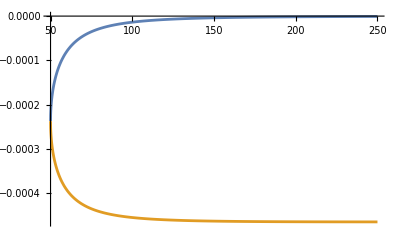

```mathematica
Plot[{tetain0[x],tetaou0[x]},{x,z,5z},PlotRange->All]
```

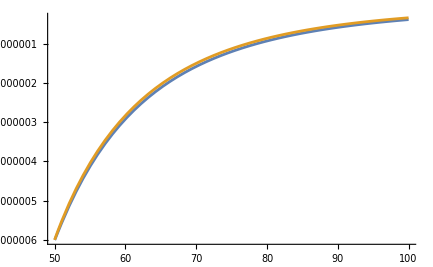

```mathematica
Plot[{qfin0[x],qfou0[x]},{x,z,2z},PlotRange->All]
```

#### auxil

```mathematica
(* derivation of tetou*)
```

```mathematica
(************)
```

```mathematica
Integrate[Sqrt[1-x^2],x,Assumptions->x>1]
```

1/2 x √(1-x^2)-ArcTan[(√(1-x^2))/(1+x)]

```mathematica
f1[x_]:= ArcTanh[1-2 x]
```

```mathematica
f2[x_]:=-Log[x/(x-1)]/2
```

```mathematica
f1[10.]
```

-0.0526803+1.5708 ⅈ

```mathematica
f2[10.]
```

-0.0526803

```mathematica
qin0t=Simplify[qin0[x]/.{x->r b1,d->k b1},Assumptions->{b1>1,x>b1}]
```

-(k ((4 k^2)/(b1^3 r^3)+(15-6 b1 r)/(b1^2 r^2)-(6 (-k^2+b1 r) √(-1+r^2))/(b1^3 r^2)+(12 (b1^2-k^2) ArcTan[r-√(-1+r^2)])/b1^3+(12 ArcTan[(1+b1 (-r+√(-1+r^2)))/(√(-1+b1^2))])/(√(-1+b1^2))+6 Log[(b1 r)/(-1+b1 r)]))/(24 b1 r^2)

```mathematica
qin01=-(k ((4 k^2)/(b1^3 r^3)+(15-6 b1 r)/(b1^2 r^2)-(6 (-k^2+b1 r) √(-1+r^2))/(b1^3 r^2)+6 Log[(b1 r)/(-1+b1 r)]))/(24 b1 r^2);
```

```mathematica
qin01s4=Normal[Series[qin01,{b1,Infinity, 4}]]
```

(k (-3+r √(-1+r^2)))/(4 b1^3 r^4)-(k (1+2 k^2+3 k^2 r √(-1+r^2)))/(12 b1^4 r^5)

```mathematica
qin014=Simplify[qin01s4/.r->x/b1/.k->d/b1,Assumptions->{x>0,b1>0}]
```

-(d (b1^3+2 b1 d^2+9 b1^3 x-3 b1 x^2 √(-b1^2+x^2)+3 d^2 x √(-1+x^2/b1^2)))/(12 b1^3 x^5)

```mathematica
rhsI1=Simplify[Coefficient[rhsI,ap[x],1]]
```

(d (-(2 d^2)/b1^2+((5-6 x) x)/(-1+x)))/(4 x^6)

```mathematica
rhsI0=Simplify[Coefficient[rhsI,ap[x],0]]
```

(d ((2 d^2)/b1^2+x/(-1+x)))/(4 x^6)

```mathematica
Simplify[rhsO+rhsI]
```

(d (2 d^2 (-1+x)+x^3+2 x^3 ap[x]+x^3 ap[x]^2))/(2 b1^2 (-1+x) x^6)

```mathematica
te[x_]:=(-Log[x/(x-1)]/2)
```

```mathematica
te2[x_]:=ArcTanh[1-2 x]
```

```mathematica
te[10.]
```

-0.0526803

```mathematica
te2[10.]
```

-0.0526803+1.5708 ⅈ

```mathematica
intou0[x_]:=1/24 d ((3 (-5+2 x))/x^2+(6 d^2 √(-b1^2+x^2))/(b1^4 x^2)-(4 d^2+6 x^2 √(-b1^2+x^2))/(b1^2 x^3)+(12 (b1^4-d^2) ArcTan[(x-√(-b1^2+x^2))/b1])/b1^5+(12 ArcTan[(1-x+√(-b1^2+x^2))/(√(-1+b1^2))])/(√(-1+b1^2))-6(Log[x/(x-1)]))/x^2
```

```mathematica
Limit[intou0[x],x->Infinity]
```

0

```mathematica
z=50.;
```

```mathematica
rhsI intfac/.rg->1
```

(((d^3 (1-√(1-b1^2/x^2)))/(2 b1^2 x^6)-(3 d √(1-b1^2/x^2))/(2 x^5)-(d (-1-√(1-b1^2/x^2)) (1-√(1-b1^2/x^2))^2)/(4 b1^2 (-1+x) x^3)) x^2)/(√(1-b1^2/x^2))

```mathematica
integrand0=(((d^3 (1-√(1-b1^2/x^2)))/(2 b1^2 x^6)-(3 d √(1-b1^2/x^2))/(2 x^5)-(d (-1-√(1-b1^2/x^2)) (1-√(1-b1^2/x^2))^2)/(4 b1^2 (-1+x) x^3)) x^2)/(√(1-b1^2/x^2));
```

```mathematica
Simplify[Integrate[integrand0,x],Assumptions->{b1>1,x>b1}]
```

1/24 d ((4 d^2)/(b1^2 x^3)+(15-6 x)/x^2-(6 (-d^2+b1^2 x) √(-b1^2+x^2))/(b1^4 x^2)+(12 (b1^4-d^2) ArcTan[(x-√(-b1^2+x^2))/b1])/b1^5+(12 ArcTan[(1-x+√(-b1^2+x^2))/(√(-1+b1^2))])/(√(-1+b1^2))-12 ArcTanh[1-2 x])

```mathematica
ter0[x_]:=1/24 d ((4 d^2)/(b1^2 x^3)+(15-6 x)/x^2-(6 (-d^2+b1^2 x) √(-b1^2+x^2))/(b1^4 x^2)+(12 (b1^4-d^2) ArcTan[(x-√(-b1^2+x^2))/b1])/b1^5+(12 ArcTan[(1-x+√(-b1^2+x^2))/(√(-1+b1^2))])/(√(-1+b1^2))-12 ArcTanh[1-2 x])
```

```mathematica
ter1[x_]:=1/24 d ((4 d^2)/(b1^2 x^3)+(15-6 x)/x^2-(6 (-d^2+b1^2 x) √(-b1^2+x^2))/(b1^4 x^2)+(12 (b1^4-d^2) ArcTan[(x-√(-b1^2+x^2))/b1])/b1^5+(12 ArcTan[(1-x+√(-b1^2+x^2))/(√(-1+b1^2))])/(√(-1+b1^2))+6 Log[x/(x-1)])
```

```mathematica
qin0[x]
```

-(d ((4 d^2)/(b1^2 x^3)+(15-6 x)/x^2+(6 (d^2-b1^2 x) √(-b1^2+x^2))/(b1^4 x^2)+(12 (b1^4-d^2) ArcTan[(x-√(-b1^2+x^2))/b1])/b1^5+(12 ArcTan[(1-x+√(-b1^2+x^2))/(√(-1+b1^2))])/(√(-1+b1^2))+6 Log[x/(-1+x)]))/(24 x^2)

```mathematica
FullSimplify[Limit[ter0[x],x->Infinity],Assumptions->b1>1]
```

1/4 d (-1/b1^2-ⅈ π+(2 ArcCsc[b1])/(√(-1+b1^2)))

```mathematica
FullSimplify[Limit[ter1[x],x->Infinity],Assumptions->b1>1]
```

1/4 d (-1/b1^2+(2 ArcCsc[b1])/(√(-1+b1^2)))

```mathematica
fun0[x_]:=1/4 d (-1/b1^2-ⅈ π+(2 ArcCsc[b1])/(√(-1+b1^2)))/x^2-ter0[x]/x^2
```

```mathematica
fun1[x_]:=1/4 d (-1/b1^2+(2 ArcCsc[b1])/(√(-1+b1^2)))/x^2-ter1[x]/x^2
```

```mathematica
difd[x_]:=Simplify[fun0[x]-fun1[x]]/d
```

```mathematica
difd[0.3]
```

0.-1.23358×10^-15 ⅈ

```mathematica
ArcTanh[√(1-x^2/b1^2)]
```

```mathematica
Solve[(Exp[al]-Exp[-al])/(Exp[al]+Exp[-al])==Sqrt[1-x^2],al]
```

{{al→ConditionalExpression[2 ⅈ π C[1]+Log[-(√(-1-√(1-x^2)))/(√(-1+√(1-x^2)))], C[1]∈ℤ]},{al→ConditionalExpression[2 ⅈ π C[1]+Log[(√(-1-√(1-x^2)))/(√(-1+√(1-x^2)))], C[1]∈ℤ]}}

```mathematica
f1[x_]:=Log[(Sqrt[x^2-1]-1)/(Sqrt[x^2-1]+1)]/2
```

```mathematica
f2[x_]:=ArcTanh[Sqrt[1-x^2]]
```

```mathematica
f1[10.]
```

-0.100844

```mathematica
f2[10.]
```

0.+1.47063 ⅈ

```mathematica
f1[x_]:=-Log[x/(x-1)]/2
```

```mathematica
f2[x_]:=ArcTanh[1-2x]
```

```mathematica
{f2[10.],f2[15.],f2[30.]}
```

{-0.0526803+1.5708 ⅈ,-0.0344964+1.5708 ⅈ,-0.0169508+1.5708 ⅈ}

```mathematica
{f1[10.],f1[15.],f1[30.]}
```

{-0.0526803,-0.0344964,-0.0169508}

```mathematica
f1[30.]
```

0.0169508

```mathematica
P[z_]:=z rg;
Q[z_]:=√((P[z]-rg)(P[z]+3rg));
k[z_]:=√((Q[z]-P[z]+3rg)/(2Q[z]));
𝒟[z_]:=√(P[z]^3/(P[z]-rg))
```

```mathematica
z=50.; d=𝒟[z]; b1=z;rg=1;
```

```mathematica
lim0
```

-0.000463595

```mathematica
fun0[z]
```

-6.00503×10^-6+0. ⅈ

```mathematica
fun1[z]
```

-6.00503×10^-6

```mathematica
lim0in
```

-0.000237123

```mathematica
Plot[{tetain0[x],tetaou0[x]},{x,z,5z},PlotRange->All]
```

-Graphics-

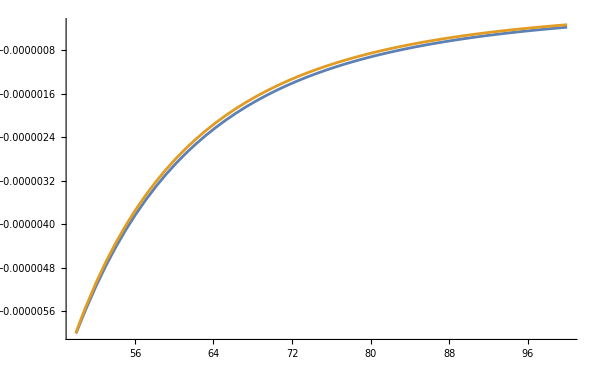

```mathematica
Plot[{qfin0[x],qfou0[x]},{x,z,2z},PlotRange->All]
```

### eq 1: θ0 term is instead of the driving force

#### q1in

```mathematica
FullSimplify[Series[tetain0[x] intfac/.{x->y b1,d->de b1},{b1,Infinity, 5}],Assumptions->{b1>1,y>1}]
```

3/8 de y (1-(y^2 ArcCsc[y])/(√(-1+y^2)))+1/(144 √(-1+y^2) b1)de (1+2 de^2) (-9 y+4 √(-1+y^2)+8 y^2 √(-1+y^2)+y^3 (-8+9 π^2+9 (Log[-1+ⅈ y-ⅈ √(-1+y^2)]-Log[1+ⅈ y-ⅈ √(-1+y^2)]) (2 ⅈ π-Log[-1+ⅈ y-ⅈ √(-1+y^2)]+Log[1+ⅈ y-ⅈ √(-1+y^2)])))+O[1/b1]^6

```mathematica
tri[y_]:=y^3 (-8+9 π^2+9 (Log[-1+ⅈ y-ⅈ √(-1+y^2)]-Log[1+ⅈ y-ⅈ √(-1+y^2)]) (2 ⅈ π-Log[-1+ⅈ y-ⅈ √(-1+y^2)]+Log[1+ⅈ y-ⅈ √(-1+y^2)]))
```

```mathematica
FullSimplify[(2 √(-1+y^2)-ⅈ y^2 Log[-ⅈ+√(-1+y^2)]+ⅈ y^2 Log[ⅈ+√(-1+y^2)]),Assumptions->y>1]
```

2 (√(-1+y^2)-y^2 ArcCsc[y])

```mathematica
FullSimplify[tri[y],Assumptions->y>10]
```

y^3 (-8+9 π^2+9 (Log[-1+ⅈ y-ⅈ √(-1+y^2)]-Log[1+ⅈ y-ⅈ √(-1+y^2)]) (2 ⅈ π-Log[-1+ⅈ y-ⅈ √(-1+y^2)]+Log[1+ⅈ y-ⅈ √(-1+y^2)]))

```mathematica
tri[10.]
```

-7909.7+0. ⅈ

## COnvergence proofs

```mathematica
ind=Simplify[Integrate[1/(x^2ap[x]),x],Assumptions->{x>0}]
```

ArcTan[(√(-b1^2+x^2))/b1]/b1

```mathematica
Limit[ind,x->Infinity]
```

1/2 √(1/b1^2) π

```mathematica
indo1=(Pi/(2 b1)-ArcTan[(√(-b1^2+x^2))/b1]/b1)
```

π/(2 b1)-ArcTan[(√(-b1^2+x^2))/b1]/b1

```mathematica
indo=Simplify[Integrate[(π/(2 b1)-ArcTan[(√(-b1^2+x^2))/b1]/b1)/(x^2ap[x]),x],Assumptions->x>0]
```

-((π-2 ArcTan[(√(-b1^2+x^2))/b1])^2)/(8 b1^2)

```mathematica
Simplify[Limit[indo,x->Infinity],Assumptions->b1>0]
```

0

```mathematica
Simplify[Integrate[(((π-2 ArcTan[(√(-b1^2+x^2))/b1])^2)/(8 b1^2))/(x^2ap[x]),x],Assumptions->x>0]
```

-((π-2 ArcTan[(√(-b1^2+x^2))/b1])^3)/(48 b1^3)

```mathematica
Simplify[Integrate[(((π-2 ArcTan[(√(-b1^2+x^2))/b1])^3)/(48 b1^3))/(x^2ap[x]),x],Assumptions->x>0]
```

-((π-2 ArcTan[(√(-b1^2+x^2))/b1])^4)/(384 b1^4)

```mathematica
Simplify[Integrate[((π)^3/(48 b1^3))/(x^2ap[x]),x],Assumptions->x>0]
```

(π^3 ∫1/(x^2 ap[x])ⅆx)/(48 b1^3)

```mathematica
Pi^3/48.
```

0.645964

```mathematica
Pi^4/384.
```

0.25367

```mathematica
f4[b_]:=b^4/(b-1/2)^4
```

```mathematica
f4[10.]
```

1.22774